%%% Some default values

```mathematica
Date[]
```

{2021,1,12,18,22,48.551907}

```mathematica
N[MachinePrecision,100]
```

15.95458977019100334632816142039813041871406371749175268945265543973673403154449900280714436226386712

%%% number of iterations :

```mathematica
nmax=500;
```

```mathematica
Take λ0[xi_,ω_] and s0[xi_,ω_] from Cho-2012, GR
```

```mathematica
λ0[xi_,ω_]:=-(1-4 ω+xi (-4+3 xi-8 (-2+xi) ω))/((-1+xi)^2 xi);
s0[xi_,ω_]:=-(-3+8 ω-32 ω^2+xi (-3-8 ω+16 ω^2))/((-1+xi)^2 xi)
```

```mathematica
FF0:=Series[λ0[xi,ω],{xi,2/5,nmax}]
GG0:=Series[s0[xi,ω],{xi,2/5,nmax}]
```

Array[CC, {nmax + 1, nmax + 1}];
Array[DD, {nmax + 1, nmax + 1}];

```mathematica
For[i=1,i<(nmax+2), i++,
CC[i,1]=Coefficient[FF0,(xi-2/5),(i-1)];
DD[i,1]=Coefficient[GG0,(xi-2/5),(i-1)]]
```

```mathematica
For[i=1,i<(nmax+2), i++,
CC[i,1]=Simplify[CC[i,1]];
DD[i,1]=Simplify[DD[i,1]]]
```

Set up iteration equations :

```mathematica
For[n=2,n<nmax+2,n++,
Print[n];
For[i=1,i<nmax+3-n,i++,

sumx=0;
sumy=0;
For[k=1,k<i+1,k++,
sumx=sumx+CC[k,1] CC[i-k+1,n-1];
sumy=sumy+DD[k,1] CC[i-k+1,n-1]
];
CC[i,n]=Expand[(i) CC[i+1,n-1]+DD[i,n-1]+sumx];
DD[i,n]=Expand[(i) DD[i+1,n-1]+sumy]
]]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

%%%%   Only the coefficients of zero order in the Taylor expansion of λn, and sn are taken.   %%%%%%

```mathematica
c0[n_]:=Expand[CC[1,n]]
d0[n_]:=Expand[DD[1,n]]
```

%%% Equations for convergence condition :

```mathematica
δ[n_,ω_]:=d0[n]c0[n-1]-d0[n-1]c0[n]
```

%%% Defining function to extract roots :

```mathematica
raices[n_]:=N[Roots[δ[n,ω]==0,ω]]
```

%%%%      Some roots:  %%
%%%%

```mathematica
R50=raices[50]
```

ω==0.0573464||ω==0.11474||ω==0.189037||ω==0.283226||ω==0.401177||ω==0.548041||ω==0.731144||ω==0.960536||ω==1.25216||ω==1.61428||ω==1.93862||ω==2.01378||ω==2.20261||ω==3.16825||ω==4.56807||ω==4.77468||ω==5.05329||ω==5.29211||ω==5.55051||ω==5.79965||ω==6.05142||ω==6.30383||ω==6.55386||ω==6.8063||ω==7.05688||ω==7.3081||ω==7.55957||ω==7.81015||ω==8.06139||ω==8.31248||ω==8.56304||ω==8.81411||ω==9.06516||ω==9.31558||ω==9.56633||ω==9.81763||ω==10.0682||ω==10.3179||ω==10.5688||ω==10.8216||ω==11.0736||ω==11.3187||ω==11.5503||ω==11.7731||ω==12.0052||ω==0.0889623-0.373672 ⅈ||ω==0.0889623+0.373672 ⅈ||ω==0.273915-0.346711 ⅈ||ω==0.273915+0.346711 ⅈ||ω==0.478277-0.301053 ⅈ||ω==0.478277+0.301053 ⅈ||ω==0.70515-0.251489 ⅈ||ω==0.70515+0.251489 ⅈ||ω==0.946845-0.207268 ⅈ||ω==0.946845+0.207268 ⅈ||ω==1.1944-0.168565 ⅈ||ω==1.1944+0.168565 ⅈ||ω==1.44672-0.13711 ⅈ||ω==1.44672+0.13711 ⅈ||ω==1.71507-0.0896243 ⅈ||ω==1.71507+0.0896243 ⅈ||ω==2.32744-0.0583875 ⅈ||ω==2.32744+0.0583875 ⅈ||ω==2.56164-0.0929885 ⅈ||ω==2.56164+0.0929885 ⅈ||ω==2.79646-0.0899289 ⅈ||ω==2.79646+0.0899289 ⅈ||ω==3.03391-0.0464412 ⅈ||ω==3.03391+0.0464412 ⅈ||ω==3.3487-0.0878265 ⅈ||ω==3.3487+0.0878265 ⅈ||ω==3.61036-0.0885713 ⅈ||ω==3.61036+0.0885713 ⅈ||ω==3.81601-0.12099 ⅈ||ω==3.81601+0.12099 ⅈ||ω==4.15859-0.0388221 ⅈ||ω==4.15859+0.0388221 ⅈ||ω==4.23245-0.163058 ⅈ||ω==4.23245+0.163058 ⅈ||ω==4.70393-0.288514 ⅈ||ω==4.70393+0.288514 ⅈ||ω==5.21884-0.405756 ⅈ||ω==5.21884+0.405756 ⅈ||ω==5.76887-0.525795 ⅈ||ω==5.76887+0.525795 ⅈ||ω==6.35907-0.647932 ⅈ||ω==6.35907+0.647932 ⅈ||ω==6.99649-0.770009 ⅈ||ω==6.99649+0.770009 ⅈ||ω==7.69156-0.8887 ⅈ||ω==7.69156+0.8887 ⅈ||ω==8.46104-0.998513 ⅈ||ω==8.46104+0.998513 ⅈ||ω==9.33577-1.08916 ⅈ||ω==9.33577+1.08916 ⅈ||ω==10.3898-1.138 ⅈ||ω==10.3898+1.138 ⅈ||ω==11.9746-1.22072 ⅈ||ω==11.9746+1.22072 ⅈ||ω==2.

50

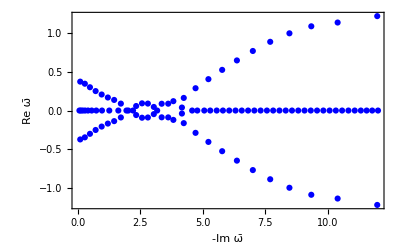

50 =n

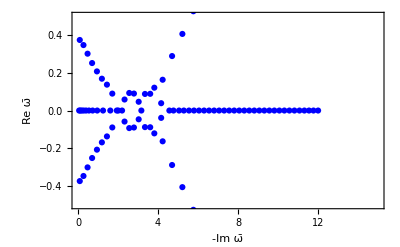

```mathematica
l50=Length[R50]-1;
d=(l50+1)/2
f50=ListPlot[
Table[{Re[R50[[k]][[2]]],Im[R50[[k]][[2]]]},{k,1,l50}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Blue]
Print[d"=n"]
h50=Show[f50,PlotRange -> {{0,15},{-1/2,1/2}},Axes->True]
```

```mathematica
R200=raices[200]
```

ω==0.0143827||ω==0.0284793||ω==0.046161||ω==0.0675676||ω==0.09278||ω==0.121882||ω==0.154971||ω==0.192164||ω==0.233598||ω==0.279424||ω==0.329812||ω==0.384943||ω==0.445011||ω==0.510198||ω==0.580705||ω==0.656817||ω==0.738718||ω==0.826429||ω==0.92067||ω==1.02136||ω==1.1282||ω==1.24363||ω==1.36338||ω==1.49551||ω==1.62645||ω==1.77792||ω==1.89634||ω==1.98482||ω==2.03121||ω==2.13578||ω==2.27848||ω==2.46542||ω==2.67076||ω==2.88384||ω==3.10396||ω==3.33582||ω==3.58592||ω==3.85661||ω==4.1432||ω==4.43951||ω==4.74976||ω==5.11771||ω==5.4744||ω==5.89678||ω==6.30275||ω==6.77084||ω==7.28663||ω==7.90445||ω==8.49972||ω==9.23259||ω==10.0453||ω==11.0434||ω==11.0946||ω==11.1454||ω==12.4383||ω==14.2704||ω==14.3382||ω==14.4416||ω==15.6269||ω==15.7902||ω==16.0932||ω==16.3226||ω==16.584||ω==16.829||ω==17.082||ω==17.331||ω==17.582||ω==17.8319||ω==18.0824||ω==18.3326||ω==18.5829||ω==18.8332||ω==19.0835||ω==19.3337||ω==19.584||ω==19.8343||ω==20.0845||ω==20.3348||ω==20.585||ω==20.8353||ω==21.0855||ω==21.3357||ω==21.5859||ω==21.8362||ω==22.0864||ω==22.3366||ω==22.5868||ω==22.837||ω==23.0872||ω==23.3374||ω==23.5876||ω==23.8378||ω==24.088||ω==24.3382||ω==24.5884||ω==24.8386||ω==25.0888||ω==25.3389||ω==25.5891||ω==25.8393||ω==26.0895||ω==26.3396||ω==26.5898||ω==26.84||ω==27.0901||ω==27.3403||ω==27.5904||ω==27.8406||ω==28.0907||ω==28.3409||ω==28.591||ω==28.8412||ω==29.0913||ω==29.3415||ω==29.5916||ω==29.8418||ω==30.0919||ω==30.342||ω==30.5922||ω==30.8423||ω==31.0924||ω==31.3426||ω==31.5927||ω==31.8428||ω==32.0929||ω==32.3431||ω==32.5932||ω==32.8433||ω==33.0934||ω==33.3436||ω==33.5937||ω==33.8438||ω==34.0939||ω==34.344||ω==34.5941||ω==34.8442||ω==35.0943||ω==35.3445||ω==35.5946||ω==35.8447||ω==36.0948||ω==36.3449||ω==36.595||ω==36.8451||ω==37.0952||ω==37.3453||ω==37.5954||ω==37.8455||ω==38.0956||ω==38.3457||ω==38.5958||ω==38.8459||ω==39.0959||ω==39.346||ω==39.5961||ω==39.8462||ω==40.0963||ω==40.3464||ω==40.5965||ω==40.8466||ω==41.0967||ω==41.3467||ω==41.5968||ω==41.8469||ω==42.097||ω==42.3471||ω==42.5972||ω==42.8472||ω==43.0973||ω==43.3474||ω==43.5975||ω==43.8476||ω==44.0976||ω==44.3477||ω==44.5978||ω==44.8479||ω==45.0979||ω==45.348||ω==45.5981||ω==45.8482||ω==46.0982||ω==46.3481||ω==46.5977||ω==46.8467||ω==47.0946||ω==47.3407||ω==47.5838||ω==47.823||ω==48.0579||ω==48.2905||ω==48.5245||ω==48.7627||ω==49.0055||ω==49.2518||ω==49.5004||ω==0.0889623-0.373672 ⅈ||ω==0.0889623+0.373672 ⅈ||ω==0.273915-0.346711 ⅈ||ω==0.273915+0.346711 ⅈ||ω==0.478277-0.301053 ⅈ||ω==0.478277+0.301053 ⅈ||ω==0.705148-0.251505 ⅈ||ω==0.705148+0.251505 ⅈ||ω==0.946845-0.207515 ⅈ||ω==0.946845+0.207515 ⅈ||ω==1.19561-0.169302 ⅈ||ω==1.19561+0.169302 ⅈ||ω==1.44785-0.133288 ⅈ||ω==1.44785+0.133288 ⅈ||ω==1.70384-0.093506 ⅈ||ω==1.70384+0.093506 ⅈ||ω==2.30618-0.0597124 ⅈ||ω==2.30618+0.0597124 ⅈ||ω==2.56121-0.0795107 ⅈ||ω==2.56121+0.0795107 ⅈ||ω==2.8123-0.0835068 ⅈ||ω==2.8123+0.0835068 ⅈ||ω==3.06557-0.0830932 ⅈ||ω==3.06557+0.0830932 ⅈ||ω==3.31968-0.0827577 ⅈ||ω==3.31968+0.0827577 ⅈ||ω==3.57187-0.0828265 ⅈ||ω==3.57187+0.0828265 ⅈ||ω==3.82133-0.0837916 ⅈ||ω==3.82133+0.0837916 ⅈ||ω==4.07078-0.0876176 ⅈ||ω==4.07078+0.0876176 ⅈ||ω==4.32388-0.0923011 ⅈ||ω==4.32388+0.0923011 ⅈ||ω==4.58074-0.0939223 ⅈ||ω==4.58074+0.0939223 ⅈ||ω==4.83825-0.0877852 ⅈ||ω==4.83825+0.0877852 ⅈ||ω==5.075-0.0784208 ⅈ||ω==5.075+0.0784208 ⅈ||ω==5.32809-0.0932511 ⅈ||ω==5.32809+0.0932511 ⅈ||ω==5.59189-0.0895981 ⅈ||ω==5.59189+0.0895981 ⅈ||ω==5.82326-0.0789734 ⅈ||ω==5.82326+0.0789734 ⅈ||ω==6.08582-0.0943981 ⅈ||ω==6.08582+0.0943981 ⅈ||ω==6.34431-0.0686187 ⅈ||ω==6.34431+0.0686187 ⅈ||ω==6.58223-0.0937861 ⅈ||ω==6.58223+0.0937861 ⅈ||ω==6.85135-0.073716 ⅈ||ω==6.85135+0.073716 ⅈ||ω==7.08285-0.0936887 ⅈ||ω==7.08285+0.0936887 ⅈ||ω==7.35259-0.0650432 ⅈ||ω==7.35259+0.0650432 ⅈ||ω==7.58841-0.0945568 ⅈ||ω==7.58841+0.0945568 ⅈ||ω==7.82179-0.0653105 ⅈ||ω==7.82179+0.0653105 ⅈ||ω==8.09942-0.0916445 ⅈ||ω==8.09942+0.0916445 ⅈ||ω==8.32592-0.087804 ⅈ||ω==8.32592+0.087804 ⅈ||ω==8.61189-0.0699194 ⅈ||ω==8.61189+0.0699194 ⅈ||ω==8.84372-0.0946062 ⅈ||ω==8.84372+0.0946062 ⅈ||ω==9.07192-0.0816936 ⅈ||ω==9.07192+0.0816936 ⅈ||ω==9.36538-0.0717732 ⅈ||ω==9.36538+0.0717732 ⅈ||ω==9.59711-0.0944305 ⅈ||ω==9.59711+0.0944305 ⅈ||ω==9.82577-0.0874373 ⅈ||ω==9.82577+0.0874373 ⅈ||ω==10.1147-0.023702 ⅈ||ω==10.1147+0.023702 ⅈ||ω==10.3607-0.0878141 ⅈ||ω==10.3607+0.0878141 ⅈ||ω==10.5911-0.0951767 ⅈ||ω==10.5911+0.0951767 ⅈ||ω==10.8222-0.0834456 ⅈ||ω==10.8222+0.0834456 ⅈ||ω==11.3683-0.0821283 ⅈ||ω==11.3683+0.0821283 ⅈ||ω==11.6018-0.0948119 ⅈ||ω==11.6018+0.0948119 ⅈ||ω==11.8347-0.0936959 ⅈ||ω==11.8347+0.0936959 ⅈ||ω==12.069-0.0797464 ⅈ||ω==12.069+0.0797464 ⅈ||ω==12.3094-0.0271083 ⅈ||ω==12.3094+0.0271083 ⅈ||ω==12.6291-0.0678276 ⅈ||ω==12.6291+0.0678276 ⅈ||ω==12.867-0.0881172 ⅈ||ω==12.867+0.0881172 ⅈ||ω==13.1039-0.0954822 ⅈ||ω==13.1039+0.0954822 ⅈ||ω==13.3411-0.0960037 ⅈ||ω==13.3411+0.0960037 ⅈ||ω==13.5788-0.0909868 ⅈ||ω==13.5788+0.0909868 ⅈ||ω==13.818-0.0801224 ⅈ||ω==13.818+0.0801224 ⅈ||ω==14.0572-0.0580487 ⅈ||ω==14.0572+0.0580487 ⅈ||ω==14.647-0.0348517 ⅈ||ω==14.647+0.0348517 ⅈ||ω==14.8759-0.0775131 ⅈ||ω==14.8759+0.0775131 ⅈ||ω==15.1511-0.0641537 ⅈ||ω==15.1511+0.0641537 ⅈ||ω==15.3364-0.101585 ⅈ||ω==15.3364+0.101585 ⅈ||ω==15.7364-0.173048 ⅈ||ω==15.7364+0.173048 ⅈ||ω==16.1957-0.285315 ⅈ||ω==16.1957+0.285315 ⅈ||ω==16.6633-0.39119 ⅈ||ω==16.6633+0.39119 ⅈ||ω==17.1379-0.498035 ⅈ||ω==17.1379+0.498035 ⅈ||ω==17.6199-0.606191 ⅈ||ω==17.6199+0.606191 ⅈ||ω==18.1095-0.715594 ⅈ||ω==18.1095+0.715594 ⅈ||ω==18.6068-0.826167 ⅈ||ω==18.6068+0.826167 ⅈ||ω==19.1122-0.93783 ⅈ||ω==19.1122+0.93783 ⅈ||ω==19.6257-1.0505 ⅈ||ω==19.6257+1.0505 ⅈ||ω==20.1476-1.16409 ⅈ||ω==20.1476+1.16409 ⅈ||ω==20.6782-1.27849 ⅈ||ω==20.6782+1.27849 ⅈ||ω==21.2177-1.39362 ⅈ||ω==21.2177+1.39362 ⅈ||ω==21.7665-1.50937 ⅈ||ω==21.7665+1.50937 ⅈ||ω==22.3247-1.62561 ⅈ||ω==22.3247+1.62561 ⅈ||ω==22.8929-1.74222 ⅈ||ω==22.8929+1.74222 ⅈ||ω==23.4712-1.85908 ⅈ||ω==23.4712+1.85908 ⅈ||ω==24.0601-1.97602 ⅈ||ω==24.0601+1.97602 ⅈ||ω==24.6601-2.09288 ⅈ||ω==24.6601+2.09288 ⅈ||ω==25.2715-2.2095 ⅈ||ω==25.2715+2.2095 ⅈ||ω==25.895-2.32566 ⅈ||ω==25.895+2.32566 ⅈ||ω==26.5311-2.44115 ⅈ||ω==26.5311+2.44115 ⅈ||ω==27.1804-2.55571 ⅈ||ω==27.1804+2.55571 ⅈ||ω==27.8435-2.66908 ⅈ||ω==27.8435+2.66908 ⅈ||ω==28.5214-2.78093 ⅈ||ω==28.5214+2.78093 ⅈ||ω==29.2148-2.8909 ⅈ||ω==29.2148+2.8909 ⅈ||ω==29.9248-2.99856 ⅈ||ω==29.9248+2.99856 ⅈ||ω==30.6524-3.10344 ⅈ||ω==30.6524+3.10344 ⅈ||ω==31.399-3.20495 ⅈ||ω==31.399+3.20495 ⅈ||ω==32.1661-3.30242 ⅈ||ω==32.1661+3.30242 ⅈ||ω==32.9553-3.39505 ⅈ||ω==32.9553+3.39505 ⅈ||ω==33.7687-3.48183 ⅈ||ω==33.7687+3.48183 ⅈ||ω==34.6088-3.56155 ⅈ||ω==34.6088+3.56155 ⅈ||ω==35.4785-3.63268 ⅈ||ω==35.4785+3.63268 ⅈ||ω==36.3816-3.69327 ⅈ||ω==36.3816+3.69327 ⅈ||ω==37.3226-3.74073 ⅈ||ω==37.3226+3.74073 ⅈ||ω==38.3075-3.77161 ⅈ||ω==38.3075+3.77161 ⅈ||ω==39.3445-3.78105 ⅈ||ω==39.3445+3.78105 ⅈ||ω==40.4449-3.76189 ⅈ||ω==40.4449+3.76189 ⅈ||ω==41.6257-3.70297 ⅈ||ω==41.6257+3.70297 ⅈ||ω==42.9147-3.58514 ⅈ||ω==42.9147+3.58514 ⅈ||ω==44.3653-3.37088 ⅈ||ω==44.3653+3.37088 ⅈ||ω==46.1155-2.96731 ⅈ||ω==46.1155+2.96731 ⅈ||ω==49.1249-2.33919 ⅈ||ω==49.1249+2.33919 ⅈ||ω==2.

200

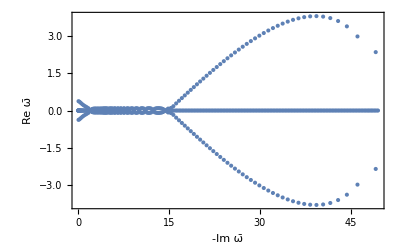

200 =n

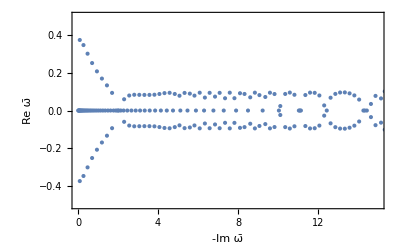

```mathematica
l200=Length[R200]-1;
d=(l200+1)/2
f200=ListPlot[
Table[{Re[R200[[k]][[2]]],Im[R200[[k]][[2]]]},{k,1,l200}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Violet]
Print[d"=n"]
h200=Show[f200,PlotRange -> {{0,15},{-1/2,1/2}},Axes->True]
```

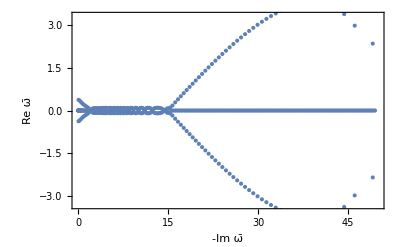

```mathematica
Show[f200,PlotRange-> {{0,50},{-3.3,3.3}}]
```

```mathematica
R300=raices[300]
```

ω==0.00959706||ω==0.0189958||ω==0.0307712||ω==0.0450022||ω==0.0617226||ω==0.0809609||ω==0.102749||ω==0.127122||ω==0.154126||ω==0.183809||ω==0.216228||ω==0.251445||ω==0.289527||ω==0.330546||ω==0.374578||ω==0.4217||ω==0.471988||ω==0.525513||ω==0.582361||ω==0.64265||ω==0.706466||ω==0.773786||ω==0.844706||ω==0.919607||ω==0.998374||ω==1.08054||ω==1.16733||ω==1.25856||ω==1.35215||ω==1.45285||ω==1.55556||ω==1.66101||ω==1.77806||ω==1.87524||ω==1.96093||ω==2.00578||ω==2.07249||ω==2.16692||ω==2.28869||ω==2.4325||ω==2.57949||ω==2.7228||ω==2.8903||ω==3.04382||ω==3.21558||ω==3.40122||ω==3.58143||ω==3.76497||ω==3.96861||ω==4.18222||ω==4.40216||ω==4.62768||ω==4.86015||ω==5.10264||ω==5.35766||ω==5.62526||ω==5.90227||ω==6.18582||ω==6.47666||ω==6.78255||ω==7.13656||ω==7.4667||ω==7.82132||ω==8.20933||ω==8.61769||ω==9.00996||ω==9.4678||ω==9.94644||ω==10.4453||ω==10.9654||ω==11.5085||ω==12.1651||ω==12.7654||ω==13.4915||ω==14.2603||ω==15.192||ω==16.1876||ω==17.2539||ω==18.7094||ω==20.4875||ω==23.1183||ω==23.331||ω==23.5889||ω==23.8382||ω==24.0874||ω==24.3387||ω==24.5881||ω==24.8388||ω==25.0887||ω==25.339||ω==25.5891||ω==25.8393||ω==26.0895||ω==26.3396||ω==26.5898||ω==26.84||ω==27.0901||ω==27.3403||ω==27.5904||ω==27.8406||ω==28.0907||ω==28.3409||ω==28.591||ω==28.8412||ω==29.0913||ω==29.3415||ω==29.5916||ω==29.8418||ω==30.0919||ω==30.342||ω==30.5922||ω==30.8423||ω==31.0924||ω==31.3426||ω==31.5927||ω==31.8428||ω==32.0929||ω==32.3431||ω==32.5932||ω==32.8433||ω==33.0934||ω==33.3436||ω==33.5937||ω==33.8438||ω==34.0939||ω==34.344||ω==34.5941||ω==34.8442||ω==35.0943||ω==35.3445||ω==35.5946||ω==35.8447||ω==36.0948||ω==36.3449||ω==36.595||ω==36.8451||ω==37.0952||ω==37.3453||ω==37.5954||ω==37.8455||ω==38.0956||ω==38.3457||ω==38.5958||ω==38.8459||ω==39.0959||ω==39.346||ω==39.5961||ω==39.8462||ω==40.0963||ω==40.3464||ω==40.5965||ω==40.8466||ω==41.0967||ω==41.3467||ω==41.5968||ω==41.8469||ω==42.097||ω==42.3471||ω==42.5972||ω==42.8472||ω==43.0973||ω==43.3474||ω==43.5975||ω==43.8476||ω==44.0976||ω==44.3477||ω==44.5978||ω==44.8479||ω==45.0979||ω==45.348||ω==45.5981||ω==45.8482||ω==46.0982||ω==46.3483||ω==46.5984||ω==46.8485||ω==47.0985||ω==47.3486||ω==47.5987||ω==47.8487||ω==48.0988||ω==48.3489||ω==48.5989||ω==48.849||ω==49.0991||ω==49.3491||ω==49.5992||ω==49.8493||ω==50.0993||ω==50.3494||ω==50.5995||ω==50.8495||ω==51.0996||ω==51.3496||ω==51.5997||ω==51.8498||ω==52.0998||ω==52.3499||ω==52.5999||ω==52.85||ω==53.1001||ω==53.3501||ω==53.6002||ω==53.8502||ω==54.1003||ω==54.3504||ω==54.6004||ω==54.8505||ω==55.1005||ω==55.3506||ω==55.6006||ω==55.8507||ω==56.1007||ω==56.3508||ω==56.6008||ω==56.8509||ω==57.101||ω==57.351||ω==57.6011||ω==57.8511||ω==58.1012||ω==58.3512||ω==58.6013||ω==58.8513||ω==59.1014||ω==59.3514||ω==59.6015||ω==59.8515||ω==60.1016||ω==60.3516||ω==60.6017||ω==60.8517||ω==61.1018||ω==61.3518||ω==61.6018||ω==61.8519||ω==62.1019||ω==62.352||ω==62.602||ω==62.8521||ω==63.1021||ω==63.3522||ω==63.6022||ω==63.8523||ω==64.1023||ω==64.3523||ω==64.6024||ω==64.8524||ω==65.1025||ω==65.3525||ω==65.6026||ω==65.8526||ω==66.1026||ω==66.3527||ω==66.6027||ω==66.8528||ω==67.1028||ω==67.3529||ω==67.6029||ω==67.8529||ω==68.103||ω==68.353||ω==68.6031||ω==68.8531||ω==69.1031||ω==69.3532||ω==69.6032||ω==69.8532||ω==70.1032||ω==70.353||ω==70.6027||ω==70.8521||ω==71.101||ω==71.3492||ω==71.5962||ω==71.8415||ω==72.0845||ω==72.3246||ω==72.5618||ω==72.797||ω==73.0325||ω==73.2703||ω==73.5114||ω==73.7557||ω==74.0024||ω==74.2508||ω==74.5002||ω==0.0889623-0.373672 ⅈ||ω==0.0889623+0.373672 ⅈ||ω==0.273915-0.346711 ⅈ||ω==0.273915+0.346711 ⅈ||ω==0.478277-0.301053 ⅈ||ω==0.478277+0.301053 ⅈ||ω==0.705148-0.251505 ⅈ||ω==0.705148+0.251505 ⅈ||ω==0.946845-0.207515 ⅈ||ω==0.946845+0.207515 ⅈ||ω==1.19561-0.1693 ⅈ||ω==1.19561+0.1693 ⅈ||ω==1.44791-0.133242 ⅈ||ω==1.44791+0.133242 ⅈ||ω==1.70401-0.0929517 ⅈ||ω==1.70401+0.0929517 ⅈ||ω==2.30398-0.0613322 ⅈ||ω==2.30398+0.0613322 ⅈ||ω==2.55986-0.0752585 ⅈ||ω==2.55986+0.0752585 ⅈ||ω==2.81485-0.0838477 ⅈ||ω==2.81485+0.0838477 ⅈ||ω==3.07-0.0846544 ⅈ||ω==3.07+0.0846544 ⅈ||ω==3.32037-0.088848 ⅈ||ω==3.32037+0.088848 ⅈ||ω==3.57283-0.0860021 ⅈ||ω==3.57283+0.0860021 ⅈ||ω==3.82734-0.0891772 ⅈ||ω==3.82734+0.0891772 ⅈ||ω==4.07644-0.0910654 ⅈ||ω==4.07644+0.0910654 ⅈ||ω==4.32541-0.0897169 ⅈ||ω==4.32541+0.0897169 ⅈ||ω==4.57587-0.0869909 ⅈ||ω==4.57587+0.0869909 ⅈ||ω==4.82754-0.0844943 ⅈ||ω==4.82754+0.0844943 ⅈ||ω==5.07909-0.0828812 ⅈ||ω==5.07909+0.0828812 ⅈ||ω==5.3294-0.0821429 ⅈ||ω==5.3294+0.0821429 ⅈ||ω==5.57859-0.0828754 ⅈ||ω==5.57859+0.0828754 ⅈ||ω==5.82836-0.0854824 ⅈ||ω==5.82836+0.0854824 ⅈ||ω==6.08039-0.0886795 ⅈ||ω==6.08039+0.0886795 ⅈ||ω==6.33491-0.0904797 ⅈ||ω==6.33491+0.0904797 ⅈ||ω==6.59097-0.0886734 ⅈ||ω==6.59097+0.0886734 ⅈ||ω==6.84466-0.079749 ⅈ||ω==6.84466+0.079749 ⅈ||ω==7.07978-0.077439 ⅈ||ω==7.07978+0.077439 ⅈ||ω==7.33356-0.0887526 ⅈ||ω==7.33356+0.0887526 ⅈ||ω==7.59445-0.0879505 ⅈ||ω==7.59445+0.0879505 ⅈ||ω==7.84357-0.0683828 ⅈ||ω==7.84357+0.0683828 ⅈ||ω==8.08213-0.0864721 ⅈ||ω==8.08213+0.0864721 ⅈ||ω==8.34678-0.0874869 ⅈ||ω==8.34678+0.0874869 ⅈ||ω==8.58369-0.0650464 ⅈ||ω==8.58369+0.0650464 ⅈ||ω==8.83794-0.08922 ⅈ||ω==8.83794+0.08922 ⅈ||ω==9.1046-0.0765999 ⅈ||ω==9.1046+0.0765999 ⅈ||ω==9.33173-0.0846099 ⅈ||ω==9.33173+0.0846099 ⅈ||ω==9.6031-0.0841011 ⅈ||ω==9.6031+0.0841011 ⅈ||ω==9.82881-0.0790981 ⅈ||ω==9.82881+0.0790981 ⅈ||ω==10.1022-0.0861348 ⅈ||ω==10.1022+0.0861348 ⅈ||ω==10.328-0.0770166 ⅈ||ω==10.328+0.0770166 ⅈ||ω==10.6041-0.0854555 ⅈ||ω==10.6041+0.0854555 ⅈ||ω==10.8292-0.0800401 ⅈ||ω==10.8292+0.0800401 ⅈ||ω==11.1088-0.0812433 ⅈ||ω==11.1088+0.0812433 ⅈ||ω==11.3339-0.0856449 ⅈ||ω==11.3339+0.0856449 ⅈ||ω==11.6143-0.0676078 ⅈ||ω==11.6143+0.0676078 ⅈ||ω==11.8433-0.0894433 ⅈ||ω==11.8433+0.0894433 ⅈ||ω==12.0753-0.0576489 ⅈ||ω==12.0753+0.0576489 ⅈ||ω==12.3568-0.085938 ⅈ||ω==12.3568+0.085938 ⅈ||ω==12.5824-0.0840261 ⅈ||ω==12.5824+0.0840261 ⅈ||ω==12.8689-0.0588675 ⅈ||ω==12.8689+0.0588675 ⅈ||ω==13.1009-0.0892071 ⅈ||ω==13.1009+0.0892071 ⅈ||ω==13.3278-0.0782692 ⅈ||ω==13.3278+0.0782692 ⅈ||ω==13.6208-0.0660079 ⅈ||ω==13.6208+0.0660079 ⅈ||ω==13.8511-0.0894752 ⅈ||ω==13.8511+0.0894752 ⅈ||ω==14.0786-0.0798177 ⅈ||ω==14.0786+0.0798177 ⅈ||ω==14.3742-0.0533113 ⅈ||ω==14.3742+0.0533113 ⅈ||ω==14.6081-0.0875258 ⅈ||ω==14.6081+0.0875258 ⅈ||ω==14.8362-0.0867576 ⅈ||ω==14.8362+0.0867576 ⅈ||ω==15.0698-0.0518914 ⅈ||ω==15.0698+0.0518914 ⅈ||ω==15.3715-0.0756186 ⅈ||ω==15.3715+0.0756186 ⅈ||ω==15.6019-0.0900096 ⅈ||ω==15.6019+0.0900096 ⅈ||ω==15.8317-0.0835406 ⅈ||ω==15.8317+0.0835406 ⅈ||ω==16.0678-0.0407024 ⅈ||ω==16.0678+0.0407024 ⅈ||ω==16.3745-0.073724 ⅈ||ω==16.3745+0.073724 ⅈ||ω==16.6067-0.089431 ⅈ||ω==16.6067+0.089431 ⅈ||ω==16.838-0.0879031 ⅈ||ω==16.838+0.0879031 ⅈ||ω==17.071-0.0687647 ⅈ||ω==17.071+0.0687647 ⅈ||ω==17.3847-0.0360726 ⅈ||ω==17.3847+0.0360726 ⅈ||ω==17.623-0.0793653 ⅈ||ω==17.623+0.0793653 ⅈ||ω==17.8567-0.0901143 ⅈ||ω==17.8567+0.0901143 ⅈ||ω==18.0902-0.0890815 ⅈ||ω==18.0902+0.0890815 ⅈ||ω==18.3246-0.0766477 ⅈ||ω==18.3246+0.0766477 ⅈ||ω==18.5628-0.0356962 ⅈ||ω==18.5628+0.0356962 ⅈ||ω==18.8862-0.05673 ⅈ||ω==18.8862+0.05673 ⅈ||ω==19.1239-0.0811228 ⅈ||ω==19.1239+0.0811228 ⅈ||ω==19.3602-0.0899677 ⅈ||ω==19.3602+0.0899677 ⅈ||ω==19.5966-0.0911517 ⅈ||ω==19.5966+0.0911517 ⅈ||ω==19.8335-0.0860221 ⅈ||ω==19.8335+0.0860221 ⅈ||ω==20.0712-0.0731851 ⅈ||ω==20.0712+0.0731851 ⅈ||ω==20.3108-0.0432271 ⅈ||ω==20.3108+0.0432271 ⅈ||ω==20.6455-0.0138576 ⅈ||ω==20.6455+0.0138576 ⅈ||ω==20.8878-0.0640275 ⅈ||ω==20.8878+0.0640275 ⅈ||ω==21.1285-0.079661 ⅈ||ω==21.1285+0.079661 ⅈ||ω==21.3684-0.0878068 ⅈ||ω==21.3684+0.0878068 ⅈ||ω==21.61-0.0914325 ⅈ||ω==21.61+0.0914325 ⅈ||ω==21.849-0.0922008 ⅈ||ω==21.849+0.0922008 ⅈ||ω==22.0947-0.0913756 ⅈ||ω==22.0947+0.0913756 ⅈ||ω==22.328-0.0850619 ⅈ||ω==22.328+0.0850619 ⅈ||ω==22.5899-0.0877974 ⅈ||ω==22.5899+0.0877974 ⅈ||ω==22.7942-0.0536855 ⅈ||ω==22.7942+0.0536855 ⅈ||ω==23.1126-0.137477 ⅈ||ω==23.1126+0.137477 ⅈ||ω==23.576-0.240468 ⅈ||ω==23.576+0.240468 ⅈ||ω==24.0354-0.343771 ⅈ||ω==24.0354+0.343771 ⅈ||ω==24.4995-0.448242 ⅈ||ω==24.4995+0.448242 ⅈ||ω==24.9683-0.553653 ⅈ||ω==24.9683+0.553653 ⅈ||ω==25.4419-0.659981 ⅈ||ω==25.4419+0.659981 ⅈ||ω==25.9205-0.767195 ⅈ||ω==25.9205+0.767195 ⅈ||ω==26.4041-0.875264 ⅈ||ω==26.4041+0.875264 ⅈ||ω==26.8927-0.984155 ⅈ||ω==26.8927+0.984155 ⅈ||ω==27.3865-1.09383 ⅈ||ω==27.3865+1.09383 ⅈ||ω==27.8855-1.20426 ⅈ||ω==27.8855+1.20426 ⅈ||ω==28.3898-1.31541 ⅈ||ω==28.3898+1.31541 ⅈ||ω==28.8996-1.42723 ⅈ||ω==28.8996+1.42723 ⅈ||ω==29.4149-1.5397 ⅈ||ω==29.4149+1.5397 ⅈ||ω==29.9358-1.65276 ⅈ||ω==29.9358+1.65276 ⅈ||ω==30.4625-1.76638 ⅈ||ω==30.4625+1.76638 ⅈ||ω==30.9949-1.88052 ⅈ||ω==30.9949+1.88052 ⅈ||ω==31.5334-1.99512 ⅈ||ω==31.5334+1.99512 ⅈ||ω==32.0779-2.11014 ⅈ||ω==32.0779+2.11014 ⅈ||ω==32.6287-2.22553 ⅈ||ω==32.6287+2.22553 ⅈ||ω==33.1858-2.34123 ⅈ||ω==33.1858+2.34123 ⅈ||ω==33.7494-2.45719 ⅈ||ω==33.7494+2.45719 ⅈ||ω==34.3197-2.57336 ⅈ||ω==34.3197+2.57336 ⅈ||ω==34.8968-2.68966 ⅈ||ω==34.8968+2.68966 ⅈ||ω==35.4809-2.80604 ⅈ||ω==35.4809+2.80604 ⅈ||ω==36.0722-2.92242 ⅈ||ω==36.0722+2.92242 ⅈ||ω==36.6709-3.03872 ⅈ||ω==36.6709+3.03872 ⅈ||ω==37.2771-3.15488 ⅈ||ω==37.2771+3.15488 ⅈ||ω==37.8912-3.27079 ⅈ||ω==37.8912+3.27079 ⅈ||ω==38.5132-3.38638 ⅈ||ω==38.5132+3.38638 ⅈ||ω==39.1436-3.50154 ⅈ||ω==39.1436+3.50154 ⅈ||ω==39.7825-3.61617 ⅈ||ω==39.7825+3.61617 ⅈ||ω==40.4302-3.73015 ⅈ||ω==40.4302+3.73015 ⅈ||ω==41.0871-3.84335 ⅈ||ω==41.0871+3.84335 ⅈ||ω==41.7534-3.95565 ⅈ||ω==41.7534+3.95565 ⅈ||ω==42.4295-4.06689 ⅈ||ω==42.4295+4.06689 ⅈ||ω==43.1159-4.17691 ⅈ||ω==43.1159+4.17691 ⅈ||ω==43.8128-4.28554 ⅈ||ω==43.8128+4.28554 ⅈ||ω==44.5209-4.39258 ⅈ||ω==44.5209+4.39258 ⅈ||ω==45.2405-4.49781 ⅈ||ω==45.2405+4.49781 ⅈ||ω==45.9721-4.60099 ⅈ||ω==45.9721+4.60099 ⅈ||ω==46.7165-4.70186 ⅈ||ω==46.7165+4.70186 ⅈ||ω==47.4742-4.80011 ⅈ||ω==47.4742+4.80011 ⅈ||ω==48.2459-4.89541 ⅈ||ω==48.2459+4.89541 ⅈ||ω==49.0325-4.98737 ⅈ||ω==49.0325+4.98737 ⅈ||ω==49.8348-5.07555 ⅈ||ω==49.8348+5.07555 ⅈ||ω==50.6539-5.15946 ⅈ||ω==50.6539+5.15946 ⅈ||ω==51.4908-5.23851 ⅈ||ω==51.4908+5.23851 ⅈ||ω==52.3468-5.31203 ⅈ||ω==52.3468+5.31203 ⅈ||ω==53.2235-5.37923 ⅈ||ω==53.2235+5.37923 ⅈ||ω==54.1224-5.43916 ⅈ||ω==54.1224+5.43916 ⅈ||ω==55.0457-5.4907 ⅈ||ω==55.0457+5.4907 ⅈ||ω==55.9955-5.53249 ⅈ||ω==55.9955+5.53249 ⅈ||ω==56.9749-5.56282 ⅈ||ω==56.9749+5.56282 ⅈ||ω==57.9871-5.57959 ⅈ||ω==57.9871+5.57959 ⅈ||ω==59.0363-5.58008 ⅈ||ω==59.0363+5.58008 ⅈ||ω==60.1281-5.56075 ⅈ||ω==60.1281+5.56075 ⅈ||ω==61.2692-5.5168 ⅈ||ω==61.2692+5.5168 ⅈ||ω==62.4691-5.44152 ⅈ||ω==62.4691+5.44152 ⅈ||ω==63.741-5.32508 ⅈ||ω==63.741+5.32508 ⅈ||ω==65.1051-5.15204 ⅈ||ω==65.1051+5.15204 ⅈ||ω==66.5943-4.89602 ⅈ||ω==66.5943+4.89602 ⅈ||ω==68.2731-4.50525 ⅈ||ω==68.2731+4.50525 ⅈ||ω==70.313-3.85219 ⅈ||ω==70.313+3.85219 ⅈ||ω==73.9641-2.84722 ⅈ||ω==73.9641+2.84722 ⅈ||ω==2.

300

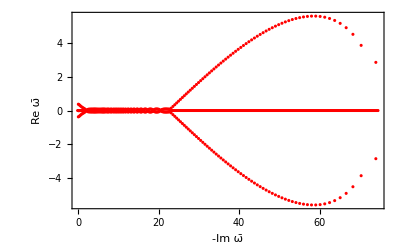

300 =n

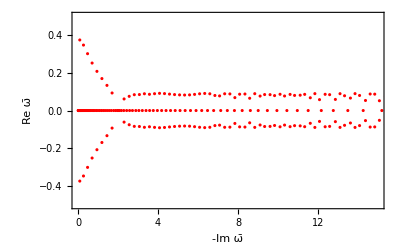

```mathematica
l300=Length[R300]-1;
d=(l300+1)/2
f300=ListPlot[
Table[{Re[R300[[k]][[2]]],Im[
R300[[k]][[2]]]},{k,1,l300}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Red]
Print[d"=n"]
h300=Show[f300,PlotRange -> {{0,15},{-1/2,1/2}},Axes->True]
```

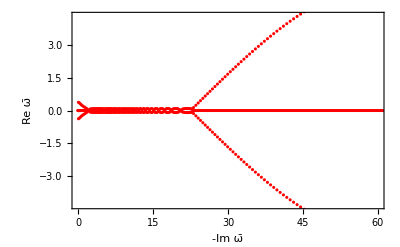

```mathematica
Show[f300,PlotRange-> {{0,60},{-4.3,4.3}}]
```

```mathematica
R400=raices[400]
```

ω==0.0072013||ω==0.0142519||ω==0.0230817||ω==0.0337463||ω==0.0462656||ω==0.060654||ω==0.0769255||ω==0.0950967||ω==0.115187||ω==0.137217||ω==0.161214||ω==0.187206||ω==0.215224||ω==0.245302||ω==0.277476||ω==0.311785||ω==0.348269||ω==0.386968||ω==0.427925||ω==0.471178||ω==0.516764||ω==0.564728||ω==0.615127||ω==0.668023||ω==0.723431||ω==0.781329||ω==0.841791||ω==0.905036||ω==0.97107||ω==1.03954||ω==1.11064||ω==1.18525||ω==1.26258||ω==1.34157||ω==1.42496||ω==1.51206||ω==1.59797||ω==1.69143||ω==1.78762||ω==1.87099||ω==1.94783||ω==1.99752||ω==2.04511||ω==2.12337||ω==2.21094||ω==2.3324||ω==2.4422||ω==2.5627||ω==2.68712||ω==2.81433||ω==2.94644||ω==3.08531||ω==3.22079||ω==3.37367||ω==3.51242||ω==3.67456||ω==3.83112||ω==3.98912||ω==4.16615||ω==4.33656||ω==4.5076||ω==4.69842||ω==4.89365||ω==5.08209||ω==5.27551||ω==5.48536||ω==5.70388||ω==5.92811||ω==6.1572||ω==6.39139||ω==6.63181||ω==6.87991||ω==7.13646||ω==7.40081||ω==7.67147||ω==7.94751||ω==8.22941||ω==8.52076||ω==8.84356||ω==9.17413||ω==9.48753||ω==9.83244||ω==10.1987||ω==10.5437||ω==10.9497||ω==11.3328||ω==11.7422||ω==12.1926||ω==12.6496||ω==13.0898||ω==13.5608||ω==14.0787||ω==14.6552||ω==15.203||ω==15.7608||ω==16.436||ω==17.0403||ω==17.7591||ω==18.5136||ω==19.4104||ω==20.2391||ω==21.2279||ω==22.2663||ω==23.5056||ω==24.9829||ω==26.7418||ω==29.2347||ω==29.3713||ω==29.4407||ω==30.8728||ω==31.0736||ω==31.3502||ω==31.5889||ω==31.8446||ω==32.0921||ω==32.3435||ω==32.593||ω==32.8434||ω==33.0934||ω==33.3436||ω==33.5937||ω==33.8438||ω==34.0939||ω==34.344||ω==34.5941||ω==34.8442||ω==35.0943||ω==35.3445||ω==35.5946||ω==35.8447||ω==36.0948||ω==36.3449||ω==36.595||ω==36.8451||ω==37.0952||ω==37.3453||ω==37.5954||ω==37.8455||ω==38.0956||ω==38.3457||ω==38.5958||ω==38.8459||ω==39.0959||ω==39.346||ω==39.5961||ω==39.8462||ω==40.0963||ω==40.3464||ω==40.5965||ω==40.8466||ω==41.0967||ω==41.3467||ω==41.5968||ω==41.8469||ω==42.097||ω==42.3471||ω==42.5972||ω==42.8472||ω==43.0973||ω==43.3474||ω==43.5975||ω==43.8476||ω==44.0976||ω==44.3477||ω==44.5978||ω==44.8479||ω==45.0979||ω==45.348||ω==45.5981||ω==45.8482||ω==46.0982||ω==46.3483||ω==46.5984||ω==46.8485||ω==47.0985||ω==47.3486||ω==47.5987||ω==47.8487||ω==48.0988||ω==48.3489||ω==48.5989||ω==48.849||ω==49.0991||ω==49.3491||ω==49.5992||ω==49.8493||ω==50.0993||ω==50.3494||ω==50.5995||ω==50.8495||ω==51.0996||ω==51.3496||ω==51.5997||ω==51.8498||ω==52.0998||ω==52.3499||ω==52.5999||ω==52.85||ω==53.1001||ω==53.3501||ω==53.6002||ω==53.8502||ω==54.1003||ω==54.3504||ω==54.6004||ω==54.8505||ω==55.1005||ω==55.3506||ω==55.6006||ω==55.8507||ω==56.1007||ω==56.3508||ω==56.6008||ω==56.8509||ω==57.101||ω==57.351||ω==57.6011||ω==57.8511||ω==58.1012||ω==58.3512||ω==58.6013||ω==58.8513||ω==59.1014||ω==59.3514||ω==59.6015||ω==59.8515||ω==60.1016||ω==60.3516||ω==60.6017||ω==60.8517||ω==61.1018||ω==61.3518||ω==61.6018||ω==61.8519||ω==62.1019||ω==62.352||ω==62.602||ω==62.8521||ω==63.1021||ω==63.3522||ω==63.6022||ω==63.8523||ω==64.1023||ω==64.3523||ω==64.6024||ω==64.8524||ω==65.1025||ω==65.3525||ω==65.6026||ω==65.8526||ω==66.1026||ω==66.3527||ω==66.6027||ω==66.8528||ω==67.1028||ω==67.3529||ω==67.6029||ω==67.8529||ω==68.103||ω==68.353||ω==68.6031||ω==68.8531||ω==69.1031||ω==69.3532||ω==69.6032||ω==69.8533||ω==70.1033||ω==70.3533||ω==70.6034||ω==70.8534||ω==71.1034||ω==71.3535||ω==71.6035||ω==71.8536||ω==72.1036||ω==72.3536||ω==72.6037||ω==72.8537||ω==73.1037||ω==73.3538||ω==73.6038||ω==73.8539||ω==74.1039||ω==74.3539||ω==74.604||ω==74.854||ω==75.104||ω==75.3541||ω==75.6041||ω==75.8541||ω==76.1042||ω==76.3542||ω==76.6042||ω==76.8543||ω==77.1043||ω==77.3543||ω==77.6044||ω==77.8544||ω==78.1044||ω==78.3545||ω==78.6045||ω==78.8545||ω==79.1046||ω==79.3546||ω==79.6046||ω==79.8547||ω==80.1047||ω==80.3547||ω==80.6048||ω==80.8548||ω==81.1048||ω==81.3548||ω==81.6049||ω==81.8549||ω==82.1049||ω==82.355||ω==82.605||ω==82.855||ω==83.1051||ω==83.3551||ω==83.6051||ω==83.8551||ω==84.1052||ω==84.3552||ω==84.6052||ω==84.8553||ω==85.1053||ω==85.3553||ω==85.6054||ω==85.8554||ω==86.1054||ω==86.3554||ω==86.6055||ω==86.8555||ω==87.1055||ω==87.3556||ω==87.6056||ω==87.8556||ω==88.1056||ω==88.3557||ω==88.6057||ω==88.8557||ω==89.1057||ω==89.3558||ω==89.6058||ω==89.8558||ω==90.1058||ω==90.3559||ω==90.6059||ω==90.8559||ω==91.106||ω==91.356||ω==91.606||ω==91.856||ω==92.1061||ω==92.3561||ω==92.6061||ω==92.8561||ω==93.1062||ω==93.3562||ω==93.6062||ω==93.8562||ω==94.1061||ω==94.3561||ω==94.6059||ω==94.8556||ω==95.105||ω==95.3542||ω==95.6028||ω==95.8508||ω==96.0978||ω==96.3434||ω==96.5872||ω==96.8287||ω==97.0679||ω==97.3053||ω==97.5419||ω==97.7795||ω==98.0193||ω==98.2617||ω==98.5065||ω==98.7532||ω==99.0014||ω==99.2505||ω==99.5001||ω==0.0889623-0.373672 ⅈ||ω==0.0889623+0.373672 ⅈ||ω==0.273915-0.346711 ⅈ||ω==0.273915+0.346711 ⅈ||ω==0.478277-0.301053 ⅈ||ω==0.478277+0.301053 ⅈ||ω==0.705148-0.251505 ⅈ||ω==0.705148+0.251505 ⅈ||ω==0.946845-0.207515 ⅈ||ω==0.946845+0.207515 ⅈ||ω==1.19561-0.169299 ⅈ||ω==1.19561+0.169299 ⅈ||ω==1.44791-0.133253 ⅈ||ω==1.44791+0.133253 ⅈ||ω==1.7039-0.0927644 ⅈ||ω==1.7039+0.0927644 ⅈ||ω==2.3015-0.0629721 ⅈ||ω==2.3015+0.0629721 ⅈ||ω==2.5608-0.0757454 ⅈ||ω==2.5608+0.0757454 ⅈ||ω==2.81552-0.0818319 ⅈ||ω==2.81552+0.0818319 ⅈ||ω==3.0682-0.0850599 ⅈ||ω==3.0682+0.0850599 ⅈ||ω==3.32043-0.087792 ⅈ||ω==3.32043+0.087792 ⅈ||ω==3.57404-0.0889671 ⅈ||ω==3.57404+0.0889671 ⅈ||ω==3.82486-0.0872856 ⅈ||ω==3.82486+0.0872856 ⅈ||ω==4.07665-0.0899836 ⅈ||ω==4.07665+0.0899836 ⅈ||ω==4.3276-0.0867179 ⅈ||ω==4.3276+0.0867179 ⅈ||ω==4.58059-0.0894564 ⅈ||ω==4.58059+0.0894564 ⅈ||ω==4.82845-0.0885501 ⅈ||ω==4.82845+0.0885501 ⅈ||ω==5.08147-0.0846129 ⅈ||ω==5.08147+0.0846129 ⅈ||ω==5.33515-0.0871591 ⅈ||ω==5.33515+0.0871591 ⅈ||ω==5.58416-0.0890711 ⅈ||ω==5.58416+0.0890711 ⅈ||ω==5.83247-0.0885247 ⅈ||ω==5.83247+0.0885247 ⅈ||ω==6.08152-0.0865709 ⅈ||ω==6.08152+0.0865709 ⅈ||ω==6.3315-0.0842342 ⅈ||ω==6.3315+0.0842342 ⅈ||ω==6.58203-0.0822804 ⅈ||ω==6.58203+0.0822804 ⅈ||ω==6.83246-0.0811411 ⅈ||ω==6.83246+0.0811411 ⅈ||ω==7.08248-0.081067 ⅈ||ω==7.08248+0.081067 ⅈ||ω==7.3325-0.0821919 ⅈ||ω==7.3325+0.0821919 ⅈ||ω==7.58333-0.0842024 ⅈ||ω==7.58333+0.0842024 ⅈ||ω==7.8356-0.0862572 ⅈ||ω==7.8356+0.0862572 ⅈ||ω==8.08941-0.0872476 ⅈ||ω==8.08941+0.0872476 ⅈ||ω==8.34425-0.0858184 ⅈ||ω==8.34425+0.0858184 ⅈ||ω==8.5983-0.0798908 ⅈ||ω==8.5983+0.0798908 ⅈ||ω==8.84062-0.0692979 ⅈ||ω==8.84062+0.0692979 ⅈ||ω==9.08337-0.0805826 ⅈ||ω==9.08337+0.0805826 ⅈ||ω==9.34024-0.0865065 ⅈ||ω==9.34024+0.0865065 ⅈ||ω==9.59945-0.0830675 ⅈ||ω==9.59945+0.0830675 ⅈ||ω==9.84524-0.0648969 ⅈ||ω==9.84524+0.0648969 ⅈ||ω==10.0848-0.0820814 ⅈ||ω==10.0848+0.0820814 ⅈ||ω==10.3467-0.0857668 ⅈ||ω==10.3467+0.0857668 ⅈ||ω==10.6041-0.0688845 ⅈ||ω==10.6041+0.0688845 ⅈ||ω==10.8343-0.0806001 ⅈ||ω==10.8343+0.0806001 ⅈ||ω==11.0992-0.0850786 ⅈ||ω==11.0992+0.0850786 ⅈ||ω==11.3483-0.0573013 ⅈ||ω==11.3483+0.0573013 ⅈ||ω==11.5891-0.0846359 ⅈ||ω==11.5891+0.0846359 ⅈ||ω==11.8571-0.0781902 ⅈ||ω==11.8571+0.0781902 ⅈ||ω==12.0824-0.0760977 ⅈ||ω==12.0824+0.0760977 ⅈ||ω==12.3519-0.0844974 ⅈ||ω==12.3519+0.0844974 ⅈ||ω==12.5822-0.0615875 ⅈ||ω==12.5822+0.0615875 ⅈ||ω==12.8476-0.0859458 ⅈ||ω==12.8476+0.0859458 ⅈ||ω==13.0991-0.0460529 ⅈ||ω==13.0991+0.0460529 ⅈ||ω==13.3454-0.0859387 ⅈ||ω==13.3454+0.0859387 ⅈ||ω==13.6093-0.0503645 ⅈ||ω==13.6093+0.0503645 ⅈ||ω==13.8457-0.0859263 ⅈ||ω==13.8457+0.0859263 ⅈ||ω==14.1049-0.0409835 ⅈ||ω==14.1049+0.0409835 ⅈ||ω==14.3486-0.0859866 ⅈ||ω==14.3486+0.0859866 ⅈ||ω==14.5803-0.0538678 ⅈ||ω==14.5803+0.0538678 ⅈ||ω==14.8542-0.0848754 ⅈ||ω==14.8542+0.0848754 ⅈ||ω==15.0797-0.0704782 ⅈ||ω==15.0797+0.0704782 ⅈ||ω==15.3622-0.0797119 ⅈ||ω==15.3622+0.0797119 ⅈ||ω==15.5866-0.0815063 ⅈ||ω==15.5866+0.0815063 ⅈ||ω==15.8699-0.0624135 ⅈ||ω==15.8699+0.0624135 ⅈ||ω==16.0983-0.0861413 ⅈ||ω==16.0983+0.0861413 ⅈ||ω==16.3271-0.0598151 ⅈ||ω==16.3271+0.0598151 ⅈ||ω==16.6132-0.0805382 ⅈ||ω==16.6132+0.0805382 ⅈ||ω==16.8383-0.0827338 ⅈ||ω==16.8383+0.0827338 ⅈ||ω==17.1218-0.0408871 ⅈ||ω==17.1218+0.0408871 ⅈ||ω==17.3573-0.0848959 ⅈ||ω==17.3573+0.0848959 ⅈ||ω==17.5832-0.0780958 ⅈ||ω==17.5832+0.0780958 ⅈ||ω==17.8752-0.0562278 ⅈ||ω==17.8752+0.0562278 ⅈ||ω==18.1059-0.085687 ⅈ||ω==18.1059+0.085687 ⅈ||ω==18.3325-0.0775087 ⅈ||ω==18.3325+0.0775087 ⅈ||ω==18.6272-0.050689 ⅈ||ω==18.6272+0.050689 ⅈ||ω==18.8596-0.0847382 ⅈ||ω==18.8596+0.0847382 ⅈ||ω==19.0867-0.0816661 ⅈ||ω==19.0867+0.0816661 ⅈ||ω==19.3252-0.0194588 ⅈ||ω==19.3252+0.0194588 ⅈ||ω==19.6184-0.0793858 ⅈ||ω==19.6184+0.0793858 ⅈ||ω==19.8466-0.0862865 ⅈ||ω==19.8466+0.0862865 ⅈ||ω==20.0762-0.067833 ⅈ||ω==20.0762+0.067833 ⅈ||ω==20.3803-0.0573314 ⅈ||ω==20.3803+0.0573314 ⅈ||ω==20.6124-0.0844759 ⅈ||ω==20.6124+0.0844759 ⅈ||ω==20.8414-0.084704 ⅈ||ω==20.8414+0.084704 ⅈ||ω==21.073-0.0605786 ⅈ||ω==21.073+0.0605786 ⅈ||ω==21.3817-0.0593219 ⅈ||ω==21.3817+0.0593219 ⅈ||ω==21.6144-0.0841143 ⅈ||ω==21.6144+0.0841143 ⅈ||ω==21.8447-0.0860768 ⅈ||ω==21.8447+0.0860768 ⅈ||ω==22.0763-0.0701048 ⅈ||ω==22.0763+0.0701048 ⅈ||ω==22.3868-0.0244182 ⅈ||ω==22.3868+0.0244182 ⅈ||ω==22.6247-0.0766722 ⅈ||ω==22.6247+0.0766722 ⅈ||ω==22.8569-0.0871531 ⅈ||ω==22.8569+0.0871531 ⅈ||ω==23.0889-0.0837561 ⅈ||ω==23.0889+0.0837561 ⅈ||ω==23.3226-0.063722 ⅈ||ω==23.3226+0.063722 ⅈ||ω==23.6398-0.0274079 ⅈ||ω==23.6398+0.0274079 ⅈ||ω==23.878-0.0745243 ⅈ||ω==23.878+0.0745243 ⅈ||ω==24.1121-0.0864117 ⅈ||ω==24.1121+0.0864117 ⅈ||ω==24.3458-0.0868609 ⅈ||ω==24.3458+0.0868609 ⅈ||ω==24.5802-0.0770582 ⅈ||ω==24.5802+0.0770582 ⅈ||ω==24.8168-0.0475017 ⅈ||ω==24.8168+0.0475017 ⅈ||ω==25.142-0.0403957 ⅈ||ω==25.142+0.0403957 ⅈ||ω==25.3802-0.0740405 ⅈ||ω==25.3802+0.0740405 ⅈ||ω==25.6164-0.0855068 ⅈ||ω==25.6164+0.0855068 ⅈ||ω==25.8524-0.0882657 ⅈ||ω==25.8524+0.0882657 ⅈ||ω==26.0887-0.0843223 ⅈ||ω==26.0887+0.0843223 ⅈ||ω==26.3258-0.0725172 ⅈ||ω==26.3258+0.0725172 ⅈ||ω==26.5645-0.0439107 ⅈ||ω==26.5645+0.0439107 ⅈ||ω==26.8975-0.0110587 ⅈ||ω==26.8975+0.0110587 ⅈ||ω==27.1387-0.0636254 ⅈ||ω==27.1387+0.0636254 ⅈ||ω==27.3779-0.079179 ⅈ||ω==27.3779+0.079179 ⅈ||ω==27.6168-0.0864435 ⅈ||ω==27.6168+0.0864435 ⅈ||ω==27.8558-0.0888848 ⅈ||ω==27.8558+0.0888848 ⅈ||ω==28.0952-0.087577 ⅈ||ω==28.0952+0.087577 ⅈ||ω==28.335-0.0826332 ⅈ||ω==28.335+0.0826332 ⅈ||ω==28.5754-0.073495 ⅈ||ω==28.5754+0.073495 ⅈ||ω==28.8161-0.0571157 ⅈ||ω==28.8161+0.0571157 ⅈ||ω==29.0592-0.0183617 ⅈ||ω==29.0592+0.0183617 ⅈ||ω==29.6444-0.0514579 ⅈ||ω==29.6444+0.0514579 ⅈ||ω==29.8986-0.0590772 ⅈ||ω==29.8986+0.0590772 ⅈ||ω==30.1209-0.081842 ⅈ||ω==30.1209+0.081842 ⅈ||ω==30.4124-0.0647841 ⅈ||ω==30.4124+0.0647841 ⅈ||ω==30.5681-0.0912966 ⅈ||ω==30.5681+0.0912966 ⅈ||ω==30.961-0.195163 ⅈ||ω==30.961+0.195163 ⅈ||ω==31.4181-0.301359 ⅈ||ω==31.4181+0.301359 ⅈ||ω==31.8773-0.404662 ⅈ||ω==31.8773+0.404662 ⅈ||ω==32.3397-0.508608 ⅈ||ω==32.3397+0.508608 ⅈ||ω==32.8057-0.613282 ⅈ||ω==32.8057+0.613282 ⅈ||ω==33.2752-0.718661 ⅈ||ω==33.2752+0.718661 ⅈ||ω==33.7484-0.824725 ⅈ||ω==33.7484+0.824725 ⅈ||ω==34.2253-0.931457 ⅈ||ω==34.2253+0.931457 ⅈ||ω==34.7059-1.03884 ⅈ||ω==34.7059+1.03884 ⅈ||ω==35.1903-1.14685 ⅈ||ω==35.1903+1.14685 ⅈ||ω==35.6785-1.25548 ⅈ||ω==35.6785+1.25548 ⅈ||ω==36.1705-1.3647 ⅈ||ω==36.1705+1.3647 ⅈ||ω==36.6664-1.4745 ⅈ||ω==36.6664+1.4745 ⅈ||ω==37.1663-1.58484 ⅈ||ω==37.1663+1.58484 ⅈ||ω==37.6701-1.69573 ⅈ||ω==37.6701+1.69573 ⅈ||ω==38.178-1.80712 ⅈ||ω==38.178+1.80712 ⅈ||ω==38.6901-1.919 ⅈ||ω==38.6901+1.919 ⅈ||ω==39.2063-2.03135 ⅈ||ω==39.2063+2.03135 ⅈ||ω==39.7267-2.14415 ⅈ||ω==39.7267+2.14415 ⅈ||ω==40.2514-2.25737 ⅈ||ω==40.2514+2.25737 ⅈ||ω==40.7804-2.37098 ⅈ||ω==40.7804+2.37098 ⅈ||ω==41.3138-2.48497 ⅈ||ω==41.3138+2.48497 ⅈ||ω==41.8518-2.5993 ⅈ||ω==41.8518+2.5993 ⅈ||ω==42.3942-2.71395 ⅈ||ω==42.3942+2.71395 ⅈ||ω==42.9413-2.82889 ⅈ||ω==42.9413+2.82889 ⅈ||ω==43.4931-2.94409 ⅈ||ω==43.4931+2.94409 ⅈ||ω==44.0497-3.05952 ⅈ||ω==44.0497+3.05952 ⅈ||ω==44.6111-3.17515 ⅈ||ω==44.6111+3.17515 ⅈ||ω==45.1774-3.29095 ⅈ||ω==45.1774+3.29095 ⅈ||ω==45.7488-3.40688 ⅈ||ω==45.7488+3.40688 ⅈ||ω==46.3253-3.52291 ⅈ||ω==46.3253+3.52291 ⅈ||ω==46.9071-3.63899 ⅈ||ω==46.9071+3.63899 ⅈ||ω==47.4941-3.7551 ⅈ||ω==47.4941+3.7551 ⅈ||ω==48.0866-3.87119 ⅈ||ω==48.0866+3.87119 ⅈ||ω==48.6846-3.98721 ⅈ||ω==48.6846+3.98721 ⅈ||ω==49.2883-4.10313 ⅈ||ω==49.2883+4.10313 ⅈ||ω==49.8978-4.2189 ⅈ||ω==49.8978+4.2189 ⅈ||ω==50.5131-4.33445 ⅈ||ω==50.5131+4.33445 ⅈ||ω==51.1345-4.44975 ⅈ||ω==51.1345+4.44975 ⅈ||ω==51.762-4.56474 ⅈ||ω==51.762+4.56474 ⅈ||ω==52.3959-4.67936 ⅈ||ω==52.3959+4.67936 ⅈ||ω==53.0362-4.79354 ⅈ||ω==53.0362+4.79354 ⅈ||ω==53.6832-4.90723 ⅈ||ω==53.6832+4.90723 ⅈ||ω==54.337-5.02035 ⅈ||ω==54.337+5.02035 ⅈ||ω==54.9977-5.13282 ⅈ||ω==54.9977+5.13282 ⅈ||ω==55.6656-5.24457 ⅈ||ω==55.6656+5.24457 ⅈ||ω==56.3409-5.35551 ⅈ||ω==56.3409+5.35551 ⅈ||ω==57.0238-5.46555 ⅈ||ω==57.0238+5.46555 ⅈ||ω==57.7146-5.5746 ⅈ||ω==57.7146+5.5746 ⅈ||ω==58.4133-5.68254 ⅈ||ω==58.4133+5.68254 ⅈ||ω==59.1204-5.78927 ⅈ||ω==59.1204+5.78927 ⅈ||ω==59.8361-5.89467 ⅈ||ω==59.8361+5.89467 ⅈ||ω==60.5607-5.9986 ⅈ||ω==60.5607+5.9986 ⅈ||ω==61.2944-6.10092 ⅈ||ω==61.2944+6.10092 ⅈ||ω==62.0377-6.20147 ⅈ||ω==62.0377+6.20147 ⅈ||ω==62.7909-6.30009 ⅈ||ω==62.7909+6.30009 ⅈ||ω==63.5543-6.3966 ⅈ||ω==63.5543+6.3966 ⅈ||ω==64.3285-6.49078 ⅈ||ω==64.3285+6.49078 ⅈ||ω==65.1138-6.58242 ⅈ||ω==65.1138+6.58242 ⅈ||ω==65.9107-6.67128 ⅈ||ω==65.9107+6.67128 ⅈ||ω==66.7199-6.75707 ⅈ||ω==66.7199+6.75707 ⅈ||ω==67.5418-6.83951 ⅈ||ω==67.5418+6.83951 ⅈ||ω==68.3772-6.91825 ⅈ||ω==68.3772+6.91825 ⅈ||ω==69.2267-6.99291 ⅈ||ω==69.2267+6.99291 ⅈ||ω==70.0911-7.06306 ⅈ||ω==70.0911+7.06306 ⅈ||ω==70.9713-7.12824 ⅈ||ω==70.9713+7.12824 ⅈ||ω==71.8683-7.18788 ⅈ||ω==71.8683+7.18788 ⅈ||ω==72.7832-7.24135 ⅈ||ω==72.7832+7.24135 ⅈ||ω==73.7171-7.28793 ⅈ||ω==73.7171+7.28793 ⅈ||ω==74.6717-7.32678 ⅈ||ω==74.6717+7.32678 ⅈ||ω==75.6483-7.35688 ⅈ||ω==75.6483+7.35688 ⅈ||ω==76.649-7.37707 ⅈ||ω==76.649+7.37707 ⅈ||ω==77.676-7.38593 ⅈ||ω==77.676+7.38593 ⅈ||ω==78.7317-7.38175 ⅈ||ω==78.7317+7.38175 ⅈ||ω==79.8194-7.3624 ⅈ||ω==79.8194+7.3624 ⅈ||ω==80.9428-7.32524 ⅈ||ω==80.9428+7.32524 ⅈ||ω==82.1066-7.26687 ⅈ||ω==82.1066+7.26687 ⅈ||ω==83.3167-7.18287 ⅈ||ω==83.3167+7.18287 ⅈ||ω==84.5811-7.06723 ⅈ||ω==84.5811+7.06723 ⅈ||ω==85.9101-6.91158 ⅈ||ω==85.9101+6.91158 ⅈ||ω==87.3187-6.70361 ⅈ||ω==87.3187+6.70361 ⅈ||ω==88.8297-6.42411 ⅈ||ω==88.8297+6.42411 ⅈ||ω==90.481-6.0402 ⅈ||ω==90.481+6.0402 ⅈ||ω==92.3473-5.48772 ⅈ||ω==92.3473+5.48772 ⅈ||ω==94.6307-4.61045 ⅈ||ω==94.6307+4.61045 ⅈ||ω==98.8276-3.27637 ⅈ||ω==98.8276+3.27637 ⅈ||ω==2.

400

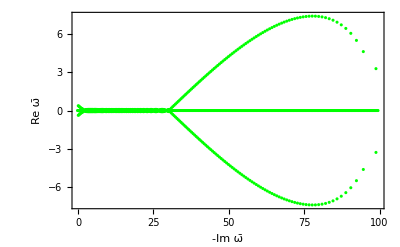

400 =n

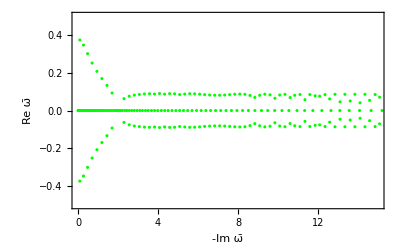

```mathematica
l400=Length[R400]-1;
d=(l400+1)/2
f400=ListPlot[
Table[{Re[R400[[k]][[2]]],Im[R400[[k]][[2]]]},{k,1,l400}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Green]
Print[d"=n"]
h400=Show[f400,PlotRange -> {{0,15},{-1/2,1/2}},Axes->True]
```

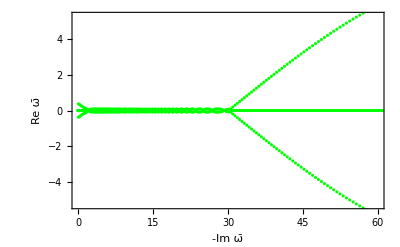

```mathematica
Show[f400,PlotRange-> {{0,60},{-5.3,5.3}}]
```

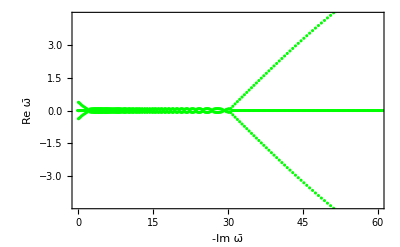

```mathematica
Show[f400,PlotRange-> {{0,60},{-4.3,4.3}}]
```

```mathematica
R500=raices[500]
```

ω==0.0057628||ω==0.0114043||ω==0.018468||ω==0.0269972||ω==0.0370057||ω==0.0485023||ω==0.0614949||ω==0.0759922||ω==0.0920044||ω==0.109543||ω==0.128622||ω==0.149256||ω==0.171463||ω==0.195261||ω==0.220671||ω==0.247713||ω==0.276412||ω==0.30679||ω==0.338873||ω==0.372687||ω==0.408256||ω==0.445606||ω==0.484759||ω==0.525739||ω==0.568574||ω==0.613302||ω==0.659959||ω==0.708559||ω==0.759085||ω==0.811551||ω==0.866063||ω==0.922744||ω==0.9815||ω==1.04211||ω==1.10474||ω==1.16998||ω==1.23756||ω==1.30644||ω==1.37743||ω==1.45243||ω==1.52869||ω==1.60448||ω==1.68633||ω==1.77173||ω==1.84762||ω==1.91884||ω==1.97996||ω==2.0141||ω==2.07445||ω==2.148||ω==2.22898||ω==2.33809||ω==2.43401||ω==2.53356||ω==2.64816||ω==2.74932||ω==2.87112||ω==2.97891||ω==3.1045||ω==3.22012||ω==3.35055||ω==3.47278||ω==3.6104||ω==3.73727||ω==3.88355||ω==4.01491||ω==4.1681||ω==4.31021||ω==4.46332||ω==4.62521||ω==4.77347||ω==4.94378||ω==5.11393||ω==5.27391||ω==5.45552||ω==5.64111||ω==5.81439||ω==6.00022||ω==6.19997||ω==6.40273||ω==6.6001||ω==6.79636||ω==7.00798||ω==7.22883||ω==7.45537||ω==7.68644||ω==7.92183||ω==8.16183||ω==8.40699||ω==8.65784||ω==8.91445||ω==9.17646||ω==9.44333||ω==9.71488||ω==9.99173||ω==10.2767||ω==10.5853||ω==10.9094||ω==11.2129||ω==11.5208||ω==11.8811||ω==12.2125||ω==12.5447||ω==12.9362||ω==13.2789||ω==13.6923||ω==14.0587||ω==14.481||ω==14.9251||ω==15.3291||ω==15.7708||ω==16.2455||ω==16.7335||ω==17.2333||ω==17.7451||ω==18.271||ω==18.8823||ω==19.4561||ω==20.0237||ω==20.7079||ω==21.4039||ω==22.0327||ω==22.778||ω==23.5656||ω==23.5913||ω==23.6554||ω==24.4643||ω==25.2949||ω==25.3591||ω==25.4055||ω==26.2722||ω==27.3139||ω==27.3275||ω==27.4329||ω==28.5023||ω==29.7692||ω==29.87||ω==29.917||ω==31.2582||ω==31.3789||ω==31.414||ω==33.0064||ω==33.1198||ω==33.1801||ω==35.2471||ω==35.3704||ω==35.4379||ω==37.9915||ω==38.068||ω==38.3548||ω==38.5952||ω==38.8447||ω==39.0971||ω==39.3452||ω==39.5966||ω==39.8459||ω==40.0965||ω==40.3463||ω==40.5965||ω==40.8466||ω==41.0967||ω==41.3467||ω==41.5968||ω==41.8469||ω==42.097||ω==42.3471||ω==42.5972||ω==42.8472||ω==43.0973||ω==43.3474||ω==43.5975||ω==43.8476||ω==44.0976||ω==44.3477||ω==44.5978||ω==44.8479||ω==45.0979||ω==45.348||ω==45.5981||ω==45.8482||ω==46.0982||ω==46.3483||ω==46.5984||ω==46.8485||ω==47.0985||ω==47.3486||ω==47.5987||ω==47.8487||ω==48.0988||ω==48.3489||ω==48.5989||ω==48.849||ω==49.0991||ω==49.3491||ω==49.5992||ω==49.8493||ω==50.0993||ω==50.3494||ω==50.5995||ω==50.8495||ω==51.0996||ω==51.3496||ω==51.5997||ω==51.8498||ω==52.0998||ω==52.3499||ω==52.5999||ω==52.85||ω==53.1001||ω==53.3501||ω==53.6002||ω==53.8502||ω==54.1003||ω==54.3504||ω==54.6004||ω==54.8505||ω==55.1005||ω==55.3506||ω==55.6006||ω==55.8507||ω==56.1007||ω==56.3508||ω==56.6008||ω==56.8509||ω==57.101||ω==57.351||ω==57.6011||ω==57.8511||ω==58.1012||ω==58.3512||ω==58.6013||ω==58.8513||ω==59.1014||ω==59.3514||ω==59.6015||ω==59.8515||ω==60.1016||ω==60.3516||ω==60.6017||ω==60.8517||ω==61.1018||ω==61.3518||ω==61.6018||ω==61.8519||ω==62.1019||ω==62.352||ω==62.602||ω==62.8521||ω==63.1021||ω==63.3522||ω==63.6022||ω==63.8523||ω==64.1023||ω==64.3523||ω==64.6024||ω==64.8524||ω==65.1025||ω==65.3525||ω==65.6026||ω==65.8526||ω==66.1026||ω==66.3527||ω==66.6027||ω==66.8528||ω==67.1028||ω==67.3529||ω==67.6029||ω==67.8529||ω==68.103||ω==68.353||ω==68.6031||ω==68.8531||ω==69.1031||ω==69.3532||ω==69.6032||ω==69.8533||ω==70.1033||ω==70.3533||ω==70.6034||ω==70.8534||ω==71.1034||ω==71.3535||ω==71.6035||ω==71.8536||ω==72.1036||ω==72.3536||ω==72.6037||ω==72.8537||ω==73.1037||ω==73.3538||ω==73.6038||ω==73.8539||ω==74.1039||ω==74.3539||ω==74.604||ω==74.854||ω==75.104||ω==75.3541||ω==75.6041||ω==75.8541||ω==76.1042||ω==76.3542||ω==76.6042||ω==76.8543||ω==77.1043||ω==77.3543||ω==77.6044||ω==77.8544||ω==78.1044||ω==78.3545||ω==78.6045||ω==78.8545||ω==79.1046||ω==79.3546||ω==79.6046||ω==79.8547||ω==80.1047||ω==80.3547||ω==80.6048||ω==80.8548||ω==81.1048||ω==81.3548||ω==81.6049||ω==81.8549||ω==82.1049||ω==82.355||ω==82.605||ω==82.855||ω==83.1051||ω==83.3551||ω==83.6051||ω==83.8551||ω==84.1052||ω==84.3552||ω==84.6052||ω==84.8553||ω==85.1053||ω==85.3553||ω==85.6054||ω==85.8554||ω==86.1054||ω==86.3554||ω==86.6055||ω==86.8555||ω==87.1055||ω==87.3556||ω==87.6056||ω==87.8556||ω==88.1056||ω==88.3557||ω==88.6057||ω==88.8557||ω==89.1057||ω==89.3558||ω==89.6058||ω==89.8558||ω==90.1058||ω==90.3559||ω==90.6059||ω==90.8559||ω==91.106||ω==91.356||ω==91.606||ω==91.856||ω==92.1061||ω==92.3561||ω==92.6061||ω==92.8561||ω==93.1062||ω==93.3562||ω==93.6062||ω==93.8562||ω==94.1063||ω==94.3563||ω==94.6063||ω==94.8563||ω==95.1064||ω==95.3564||ω==95.6064||ω==95.8564||ω==96.1065||ω==96.3565||ω==96.6065||ω==96.8565||ω==97.1066||ω==97.3566||ω==97.6066||ω==97.8566||ω==98.1066||ω==98.3567||ω==98.6067||ω==98.8567||ω==99.1067||ω==99.3568||ω==99.6068||ω==99.8568||ω==100.107||ω==100.357||ω==100.607||ω==100.857||ω==101.107||ω==101.357||ω==101.607||ω==101.857||ω==102.107||ω==102.357||ω==102.607||ω==102.857||ω==103.107||ω==103.357||ω==103.607||ω==103.857||ω==104.107||ω==104.357||ω==104.607||ω==104.857||ω==105.107||ω==105.357||ω==105.607||ω==105.857||ω==106.107||ω==106.357||ω==106.607||ω==106.857||ω==107.107||ω==107.357||ω==107.607||ω==107.857||ω==108.108||ω==108.358||ω==108.608||ω==108.858||ω==109.108||ω==109.358||ω==109.608||ω==109.858||ω==110.108||ω==110.358||ω==110.608||ω==110.858||ω==111.108||ω==111.358||ω==111.608||ω==111.858||ω==112.108||ω==112.358||ω==112.608||ω==112.858||ω==113.108||ω==113.358||ω==113.608||ω==113.858||ω==114.108||ω==114.358||ω==114.608||ω==114.858||ω==115.108||ω==115.358||ω==115.608||ω==115.858||ω==116.108||ω==116.358||ω==116.608||ω==116.858||ω==117.108||ω==117.358||ω==117.608||ω==117.858||ω==118.108||ω==118.358||ω==118.608||ω==118.858||ω==119.108||ω==119.357||ω==119.607||ω==119.856||ω==120.104||ω==120.352||ω==120.6||ω==120.846||ω==121.09||ω==121.333||ω==121.575||ω==121.814||ω==122.052||ω==122.29||ω==122.529||ω==122.77||ω==123.013||ω==123.257||ω==123.504||ω==123.752||ω==124.001||ω==124.25||ω==124.5||ω==0.0889623-0.373672 ⅈ||ω==0.0889623+0.373672 ⅈ||ω==0.273915-0.346711 ⅈ||ω==0.273915+0.346711 ⅈ||ω==0.478277-0.301053 ⅈ||ω==0.478277+0.301053 ⅈ||ω==0.705148-0.251505 ⅈ||ω==0.705148+0.251505 ⅈ||ω==0.946845-0.207515 ⅈ||ω==0.946845+0.207515 ⅈ||ω==1.19561-0.169299 ⅈ||ω==1.19561+0.169299 ⅈ||ω==1.44791-0.133252 ⅈ||ω==1.44791+0.133252 ⅈ||ω==1.70387-0.092812 ⅈ||ω==1.70387+0.092812 ⅈ||ω==2.30199-0.0634526 ⅈ||ω==2.30199+0.0634526 ⅈ||ω==2.56125-0.0765232 ⅈ||ω==2.56125+0.0765232 ⅈ||ω==2.8153-0.0829617 ⅈ||ω==2.8153+0.0829617 ⅈ||ω==3.06826-0.085767 ⅈ||ω==3.06826+0.085767 ⅈ||ω==3.32074-0.0872519 ⅈ||ω==3.32074+0.0872519 ⅈ||ω==3.57273-0.0882384 ⅈ||ω==3.57273+0.0882384 ⅈ||ω==3.82465-0.0891031 ⅈ||ω==3.82465+0.0891031 ⅈ||ω==4.07712-0.0892952 ⅈ||ω==4.07712+0.0892952 ⅈ||ω==4.32871-0.0876967 ⅈ||ω==4.32871+0.0876967 ⅈ||ω==4.57817-0.0882978 ⅈ||ω==4.57817+0.0882978 ⅈ||ω==4.83155-0.0884318 ⅈ||ω==4.83155+0.0884318 ⅈ||ω==5.08008-0.0866608 ⅈ||ω==5.08008+0.0866608 ⅈ||ω==5.33395-0.0875988 ⅈ||ω==5.33395+0.0875988 ⅈ||ω==5.5815-0.0869684 ⅈ||ω==5.5815+0.0869684 ⅈ||ω==5.83551-0.0840412 ⅈ||ω==5.83551+0.0840412 ⅈ||ω==6.08593-0.0874128 ⅈ||ω==6.08593+0.0874128 ⅈ||ω==6.3333-0.0859764 ⅈ||ω==6.3333+0.0859764 ⅈ||ω==6.5851-0.0813863 ⅈ||ω==6.5851+0.0813863 ⅈ||ω==6.84002-0.0825754 ⅈ||ω==6.84002+0.0825754 ⅈ||ω==7.09008-0.085469 ⅈ||ω==7.09008+0.085469 ⅈ||ω==7.33844-0.0863122 ⅈ||ω==7.33844+0.0863122 ⅈ||ω==7.58685-0.0856512 ⅈ||ω==7.58685+0.0856512 ⅈ||ω==7.83582-0.0842452 ⅈ||ω==7.83582+0.0842452 ⅈ||ω==8.08538-0.0827213 ⅈ||ω==8.08538+0.0827213 ⅈ||ω==8.33531-0.0815491 ⅈ||ω==8.33531+0.0815491 ⅈ||ω==8.58544-0.0810288 ⅈ||ω==8.58544+0.0810288 ⅈ||ω==8.83575-0.0812811 ⅈ||ω==8.83575+0.0812811 ⅈ||ω==9.0865-0.0822073 ⅈ||ω==9.0865+0.0822073 ⅈ||ω==9.338-0.0834556 ⅈ||ω==9.338+0.0834556 ⅈ||ω==9.59048-0.0844557 ⅈ||ω==9.59048+0.0844557 ⅈ||ω==9.84393-0.0844627 ⅈ||ω==9.84393+0.0844627 ⅈ||ω==10.0979-0.082487 ⅈ||ω==10.0979+0.082487 ⅈ||ω==10.351-0.0769787 ⅈ||ω==10.351+0.0769787 ⅈ||ω==10.5955-0.0670708 ⅈ||ω==10.5955+0.0670708 ⅈ||ω==10.8356-0.0753901 ⅈ||ω==10.8356+0.0753901 ⅈ||ω==11.0898-0.0827305 ⅈ||ω==11.0898+0.0827305 ⅈ||ω==11.3476-0.083483 ⅈ||ω==11.3476+0.083483 ⅈ||ω==11.6043-0.0755055 ⅈ||ω==11.6043+0.0755055 ⅈ||ω==11.8375-0.0661824 ⅈ||ω==11.8375+0.0661824 ⅈ||ω==12.0891-0.0814293 ⅈ||ω==12.0891+0.0814293 ⅈ||ω==12.35-0.0827595 ⅈ||ω==12.35+0.0827595 ⅈ||ω==12.6064-0.0674614 ⅈ||ω==12.6064+0.0674614 ⅈ||ω==12.8358-0.0759673 ⅈ||ω==12.8358+0.0759673 ⅈ||ω==13.0979-0.0835164 ⅈ||ω==13.0979+0.0835164 ⅈ||ω==13.3588-0.0697165 ⅈ||ω==13.3588+0.0697165 ⅈ||ω==13.5857-0.075658 ⅈ||ω==13.5857+0.075658 ⅈ||ω==13.8506-0.0830011 ⅈ||ω==13.8506+0.0830011 ⅈ||ω==14.108-0.0588444 ⅈ||ω==14.108+0.0588444 ⅈ||ω==14.3399-0.0807691 ⅈ||ω==14.3399+0.0807691 ⅈ||ω==14.6082-0.0782635 ⅈ||ω==14.6082+0.0782635 ⅈ||ω==14.8338-0.0683084 ⅈ||ω==14.8338+0.0683084 ⅈ||ω==15.1009-0.0831417 ⅈ||ω==15.1009+0.0831417 ⅈ||ω==15.3552-0.0480217 ⅈ||ω==15.3552+0.0480217 ⅈ||ω==15.5946-0.0828236 ⅈ||ω==15.5946+0.0828236 ⅈ||ω==15.8646-0.0662139 ⅈ||ω==15.8646+0.0662139 ⅈ||ω==16.0903-0.0805277 ⅈ||ω==16.0903+0.0805277 ⅈ||ω==16.3641-0.0726187 ⅈ||ω==16.3641+0.0726187 ⅈ||ω==16.5879-0.07832 ⅈ||ω==16.5879+0.07832 ⅈ||ω==16.8638-0.0746988 ⅈ||ω==16.8638+0.0746988 ⅈ||ω==17.0873-0.0776045 ⅈ||ω==17.0873+0.0776045 ⅈ||ω==17.3649-0.0739998 ⅈ||ω==17.3649+0.0739998 ⅈ||ω==17.5885-0.0788067 ⅈ||ω==17.5885+0.0788067 ⅈ||ω==17.8674-0.0700759 ⅈ||ω==17.8674+0.0700759 ⅈ||ω==18.0919-0.0812067 ⅈ||ω==18.0919+0.0812067 ⅈ||ω==18.3702-0.0597641 ⅈ||ω==18.3702+0.0597641 ⅈ||ω==18.5976-0.0832665 ⅈ||ω==18.5976+0.0832665 ⅈ||ω==18.8374-0.031603 ⅈ||ω==18.8374+0.031603 ⅈ||ω==19.1059-0.0828723 ⅈ||ω==19.1059+0.0828723 ⅈ||ω==19.3312-0.0667067 ⅈ||ω==19.3312+0.0667067 ⅈ||ω==19.6159-0.0766133 ⅈ||ω==19.6159+0.0766133 ⅈ||ω==19.84-0.0799226 ⅈ||ω==19.84+0.0799226 ⅈ||ω==20.1239-0.0533067 ⅈ||ω==20.1239+0.0533067 ⅈ||ω==20.3535-0.083621 ⅈ||ω==20.3535+0.083621 ⅈ||ω==20.5799-0.0642827 ⅈ||ω==20.5799+0.0642827 ⅈ||ω==20.8689-0.0747044 ⅈ||ω==20.8689+0.0747044 ⅈ||ω==21.094-0.0821712 ⅈ||ω==21.094+0.0821712 ⅈ||ω==21.3305-0.0288307 ⅈ||ω==21.3305+0.0288307 ⅈ||ω==21.6133-0.0806521 ⅈ||ω==21.6133+0.0806521 ⅈ||ω==21.8385-0.0788278 ⅈ||ω==21.8385+0.0788278 ⅈ||ω==22.1276-0.0399512 ⅈ||ω==22.1276+0.0399512 ⅈ||ω==22.361-0.0822369 ⅈ||ω==22.361+0.0822369 ⅈ||ω==22.5869-0.077464 ⅈ||ω==22.5869+0.077464 ⅈ||ω==22.8794-0.0400318 ⅈ||ω==22.8794+0.0400318 ⅈ||ω==23.1128-0.0818015 ⅈ||ω==23.1128+0.0818015 ⅈ||ω==23.3391-0.0794569 ⅈ||ω==23.3391+0.0794569 ⅈ||ω==23.8686-0.0784887 ⅈ||ω==23.8686+0.0784887 ⅈ||ω==24.0957-0.0830179 ⅈ||ω==24.0957+0.0830179 ⅈ||ω==24.3258-0.056659 ⅈ||ω==24.3258+0.056659 ⅈ||ω==24.6278-0.0672525 ⅈ||ω==24.6278+0.0672525 ⅈ||ω==24.857-0.0841993 ⅈ||ω==24.857+0.0841993 ⅈ||ω==25.0852-0.0762473 ⅈ||ω==25.0852+0.0762473 ⅈ||ω==25.6225-0.0764738 ⅈ||ω==25.6225+0.0764738 ⅈ||ω==25.8515-0.0845177 ⅈ||ω==25.8515+0.0845177 ⅈ||ω==26.0811-0.0715907 ⅈ||ω==26.0811+0.0715907 ⅈ||ω==26.3865-0.0255807 ⅈ||ω==26.3865+0.0255807 ⅈ||ω==26.6228-0.0770892 ⅈ||ω==26.6228+0.0770892 ⅈ||ω==26.8529-0.0848032 ⅈ||ω==26.8529+0.0848032 ⅈ||ω==27.0832-0.0746884 ⅈ||ω==27.0832+0.0746884 ⅈ||ω==27.6296-0.0700815 ⅈ||ω==27.6296+0.0700815 ⅈ||ω==27.8613-0.0842201 ⅈ||ω==27.8613+0.0842201 ⅈ||ω==28.0923-0.0820884 ⅈ||ω==28.0923+0.0820884 ⅈ||ω==28.325-0.0617886 ⅈ||ω==28.325+0.0617886 ⅈ||ω==28.6405-0.0348622 ⅈ||ω==28.6405+0.0348622 ⅈ||ω==28.8767-0.0753898 ⅈ||ω==28.8767+0.0753898 ⅈ||ω==29.1093-0.0850134 ⅈ||ω==29.1093+0.0850134 ⅈ||ω==29.3417-0.0820043 ⅈ||ω==29.3417+0.0820043 ⅈ||ω==29.5754-0.0641714 ⅈ||ω==29.5754+0.0641714 ⅈ||ω==30.1332-0.0683883 ⅈ||ω==30.1332+0.0683883 ⅈ||ω==30.3677-0.0829151 ⅈ||ω==30.3677+0.0829151 ⅈ||ω==30.6016-0.0854248 ⅈ||ω==30.6016+0.0854248 ⅈ||ω==30.8359-0.0784304 ⅈ||ω==30.8359+0.0784304 ⅈ||ω==31.0716-0.0568106 ⅈ||ω==31.0716+0.0568106 ⅈ||ω==31.6362-0.0658092 ⅈ||ω==31.6362+0.0658092 ⅈ||ω==31.8725-0.0810742 ⅈ||ω==31.8725+0.0810742 ⅈ||ω==32.1083-0.0859593 ⅈ||ω==32.1083+0.0859593 ⅈ||ω==32.3443-0.0837847 ⅈ||ω==32.3443+0.0837847 ⅈ||ω==32.5808-0.0740622 ⅈ||ω==32.5808+0.0740622 ⅈ||ω==32.8186-0.0505279 ⅈ||ω==32.8186+0.0505279 ⅈ||ω==33.3914-0.0588096 ⅈ||ω==33.3914+0.0588096 ⅈ||ω==33.63-0.0764446 ⅈ||ω==33.63+0.0764446 ⅈ||ω==33.8681-0.0842737 ⅈ||ω==33.8681+0.0842737 ⅈ||ω==34.1063-0.0865585 ⅈ||ω==34.1063+0.0865585 ⅈ||ω==34.3447-0.084386 ⅈ||ω==34.3447+0.084386 ⅈ||ω==34.5835-0.0775539 ⅈ||ω==34.5835+0.0775539 ⅈ||ω==34.8229-0.0641584 ⅈ||ω==34.8229+0.0641584 ⅈ||ω==35.0636-0.0346085 ⅈ||ω==35.0636+0.0346085 ⅈ||ω==35.647-0.0497536 ⅈ||ω==35.647+0.0497536 ⅈ||ω==35.8885-0.0687142 ⅈ||ω==35.8885+0.0687142 ⅈ||ω==36.1295-0.0787618 ⅈ||ω==36.1295+0.0787618 ⅈ||ω==36.371-0.0842106 ⅈ||ω==36.371+0.0842106 ⅈ||ω==36.6117-0.0868343 ⅈ||ω==36.6117+0.0868343 ⅈ||ω==36.8548-0.0872582 ⅈ||ω==36.8548+0.0872582 ⅈ||ω==37.0938-0.0848759 ⅈ||ω==37.0938+0.0848759 ⅈ||ω==37.3423-0.0835069 ⅈ||ω==37.3423+0.0835069 ⅈ||ω==37.572-0.0709956 ⅈ||ω==37.572+0.0709956 ⅈ||ω==37.8449-0.0822581 ⅈ||ω==37.8449+0.0822581 ⅈ||ω==38.3504-0.159977 ⅈ||ω==38.3504+0.159977 ⅈ||ω==38.8059-0.261183 ⅈ||ω==38.8059+0.261183 ⅈ||ω==39.2617-0.363648 ⅈ||ω==39.2617+0.363648 ⅈ||ω==39.7203-0.466723 ⅈ||ω==39.7203+0.466723 ⅈ||ω==40.1818-0.570373 ⅈ||ω==40.1818+0.570373 ⅈ||ω==40.6461-0.674601 ⅈ||ω==40.6461+0.674601 ⅈ||ω==41.1132-0.779399 ⅈ||ω==41.1132+0.779399 ⅈ||ω==41.5832-0.884755 ⅈ||ω==41.5832+0.884755 ⅈ||ω==42.0562-0.990658 ⅈ||ω==42.0562+0.990658 ⅈ||ω==42.5321-1.0971 ⅈ||ω==42.5321+1.0971 ⅈ||ω==43.0109-1.20406 ⅈ||ω==43.0109+1.20406 ⅈ||ω==43.4927-1.31154 ⅈ||ω==43.4927+1.31154 ⅈ||ω==43.9776-1.41951 ⅈ||ω==43.9776+1.41951 ⅈ||ω==44.4655-1.52798 ⅈ||ω==44.4655+1.52798 ⅈ||ω==44.9564-1.63692 ⅈ||ω==44.9564+1.63692 ⅈ||ω==45.4505-1.74633 ⅈ||ω==45.4505+1.74633 ⅈ||ω==45.9477-1.85618 ⅈ||ω==45.9477+1.85618 ⅈ||ω==46.4481-1.96648 ⅈ||ω==46.4481+1.96648 ⅈ||ω==46.9517-2.0772 ⅈ||ω==46.9517+2.0772 ⅈ||ω==47.4585-2.18833 ⅈ||ω==47.4585+2.18833 ⅈ||ω==47.9686-2.29986 ⅈ||ω==47.9686+2.29986 ⅈ||ω==48.482-2.41177 ⅈ||ω==48.482+2.41177 ⅈ||ω==48.9987-2.52405 ⅈ||ω==48.9987+2.52405 ⅈ||ω==49.5188-2.63668 ⅈ||ω==49.5188+2.63668 ⅈ||ω==50.0423-2.74966 ⅈ||ω==50.0423+2.74966 ⅈ||ω==50.5693-2.86295 ⅈ||ω==50.5693+2.86295 ⅈ||ω==51.0998-2.97656 ⅈ||ω==51.0998+2.97656 ⅈ||ω==51.6338-3.09045 ⅈ||ω==51.6338+3.09045 ⅈ||ω==52.1714-3.20462 ⅈ||ω==52.1714+3.20462 ⅈ||ω==52.7126-3.31904 ⅈ||ω==52.7126+3.31904 ⅈ||ω==53.2576-3.4337 ⅈ||ω==53.2576+3.4337 ⅈ||ω==53.8062-3.54859 ⅈ||ω==53.8062+3.54859 ⅈ||ω==54.3586-3.66367 ⅈ||ω==54.3586+3.66367 ⅈ||ω==54.9148-3.77894 ⅈ||ω==54.9148+3.77894 ⅈ||ω==55.4749-3.89436 ⅈ||ω==55.4749+3.89436 ⅈ||ω==56.039-4.00993 ⅈ||ω==56.039+4.00993 ⅈ||ω==56.607-4.12562 ⅈ||ω==56.607+4.12562 ⅈ||ω==57.179-4.24141 ⅈ||ω==57.179+4.24141 ⅈ||ω==57.7552-4.35727 ⅈ||ω==57.7552+4.35727 ⅈ||ω==58.3355-4.47318 ⅈ||ω==58.3355+4.47318 ⅈ||ω==58.9201-4.58911 ⅈ||ω==58.9201+4.58911 ⅈ||ω==59.5089-4.70505 ⅈ||ω==59.5089+4.70505 ⅈ||ω==60.1021-4.82096 ⅈ||ω==60.1021+4.82096 ⅈ||ω==60.6998-4.93681 ⅈ||ω==60.6998+4.93681 ⅈ||ω==61.3019-5.05259 ⅈ||ω==61.3019+5.05259 ⅈ||ω==61.9087-5.16825 ⅈ||ω==61.9087+5.16825 ⅈ||ω==62.5201-5.28376 ⅈ||ω==62.5201+5.28376 ⅈ||ω==63.1362-5.3991 ⅈ||ω==63.1362+5.3991 ⅈ||ω==63.7572-5.51423 ⅈ||ω==63.7572+5.51423 ⅈ||ω==64.383-5.62911 ⅈ||ω==64.383+5.62911 ⅈ||ω==65.0139-5.74371 ⅈ||ω==65.0139+5.74371 ⅈ||ω==65.6499-5.85799 ⅈ||ω==65.6499+5.85799 ⅈ||ω==66.2911-5.9719 ⅈ||ω==66.2911+5.9719 ⅈ||ω==66.9377-6.08541 ⅈ||ω==66.9377+6.08541 ⅈ||ω==67.5896-6.19847 ⅈ||ω==67.5896+6.19847 ⅈ||ω==68.2471-6.31103 ⅈ||ω==68.2471+6.31103 ⅈ||ω==68.9102-6.42305 ⅈ||ω==68.9102+6.42305 ⅈ||ω==69.5791-6.53446 ⅈ||ω==69.5791+6.53446 ⅈ||ω==70.2539-6.64523 ⅈ||ω==70.2539+6.64523 ⅈ||ω==70.9348-6.75528 ⅈ||ω==70.9348+6.75528 ⅈ||ω==71.6218-6.86455 ⅈ||ω==71.6218+6.86455 ⅈ||ω==72.3152-6.97299 ⅈ||ω==72.3152+6.97299 ⅈ||ω==73.0151-7.08052 ⅈ||ω==73.0151+7.08052 ⅈ||ω==73.7216-7.18707 ⅈ||ω==73.7216+7.18707 ⅈ||ω==74.435-7.29256 ⅈ||ω==74.435+7.29256 ⅈ||ω==75.1553-7.3969 ⅈ||ω==75.1553+7.3969 ⅈ||ω==75.8829-7.50002 ⅈ||ω==75.8829+7.50002 ⅈ||ω==76.6179-7.60182 ⅈ||ω==76.6179+7.60182 ⅈ||ω==77.3606-7.70219 ⅈ||ω==77.3606+7.70219 ⅈ||ω==78.1111-7.80102 ⅈ||ω==78.1111+7.80102 ⅈ||ω==78.8697-7.89821 ⅈ||ω==78.8697+7.89821 ⅈ||ω==79.6367-7.99363 ⅈ||ω==79.6367+7.99363 ⅈ||ω==80.4123-8.08713 ⅈ||ω==80.4123+8.08713 ⅈ||ω==81.1969-8.17859 ⅈ||ω==81.1969+8.17859 ⅈ||ω==81.9907-8.26784 ⅈ||ω==81.9907+8.26784 ⅈ||ω==82.7941-8.3547 ⅈ||ω==82.7941+8.3547 ⅈ||ω==83.6074-8.43901 ⅈ||ω==83.6074+8.43901 ⅈ||ω==84.4311-8.52055 ⅈ||ω==84.4311+8.52055 ⅈ||ω==85.2656-8.5991 ⅈ||ω==85.2656+8.5991 ⅈ||ω==86.1112-8.67443 ⅈ||ω==86.1112+8.67443 ⅈ||ω==86.9686-8.74626 ⅈ||ω==86.9686+8.74626 ⅈ||ω==87.8382-8.81431 ⅈ||ω==87.8382+8.81431 ⅈ||ω==88.7206-8.87825 ⅈ||ω==88.7206+8.87825 ⅈ||ω==89.6164-8.93772 ⅈ||ω==89.6164+8.93772 ⅈ||ω==90.5264-8.99232 ⅈ||ω==90.5264+8.99232 ⅈ||ω==91.4513-9.0416 ⅈ||ω==91.4513+9.0416 ⅈ||ω==92.392-9.08504 ⅈ||ω==92.392+9.08504 ⅈ||ω==93.3494-9.12208 ⅈ||ω==93.3494+9.12208 ⅈ||ω==94.3245-9.15206 ⅈ||ω==94.3245+9.15206 ⅈ||ω==95.3186-9.17423 ⅈ||ω==95.3186+9.17423 ⅈ||ω==96.3329-9.18772 ⅈ||ω==96.3329+9.18772 ⅈ||ω==97.3691-9.19153 ⅈ||ω==97.3691+9.19153 ⅈ||ω==98.4288-9.18446 ⅈ||ω==98.4288+9.18446 ⅈ||ω==99.5142-9.16512 ⅈ||ω==99.5142+9.16512 ⅈ||ω==100.628-9.13182 ⅈ||ω==100.628+9.13182 ⅈ||ω==101.772-9.08253 ⅈ||ω==101.772+9.08253 ⅈ||ω==102.95-9.01473 ⅈ||ω==102.95+9.01473 ⅈ||ω==104.167-8.92528 ⅈ||ω==104.167+8.92528 ⅈ||ω==105.427-8.81014 ⅈ||ω==105.427+8.81014 ⅈ||ω==106.736-8.66407 ⅈ||ω==106.736+8.66407 ⅈ||ω==108.105-8.47994 ⅈ||ω==108.105+8.47994 ⅈ||ω==109.543-8.24785 ⅈ||ω==109.543+8.24785 ⅈ||ω==111.068-7.95322 ⅈ||ω==111.068+7.95322 ⅈ||ω==112.705-7.57334 ⅈ||ω==112.705+7.57334 ⅈ||ω==114.496-7.06948 ⅈ||ω==114.496+7.06948 ⅈ||ω==116.526-6.36653 ⅈ||ω==116.526+6.36653 ⅈ||ω==119.026-5.28412 ⅈ||ω==119.026+5.28412 ⅈ||ω==123.707-3.65483 ⅈ||ω==123.707+3.65483 ⅈ||ω==2.

500

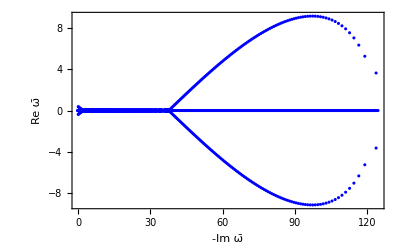

500 =n

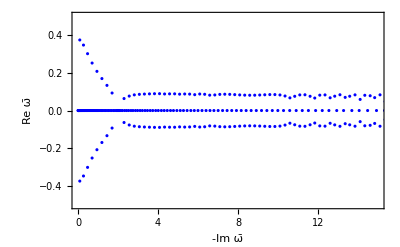

```mathematica
l500=Length[R500]-1;
d=(l500+1)/2
f500=ListPlot[
Table[{Re[R500[[k]][[2]]],Im[R500[[k]][[2]]]},{k,1,l500}],Frame->True,FrameLabel->{-Im ω̄ ,Re ω̄ },PlotRange -> All,PlotStyle->Blue]
Print[d"=n"]
h500=Show[f500,PlotRange -> {{0,15},{-0.5,0.5}},Axes->True]
```

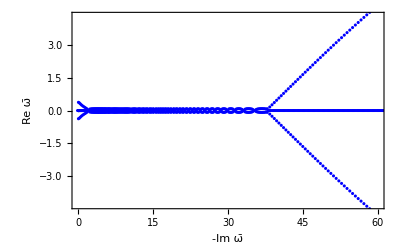

```mathematica
Show[f500,PlotRange->{{0,60}, {-4.3,4.3}}]
```

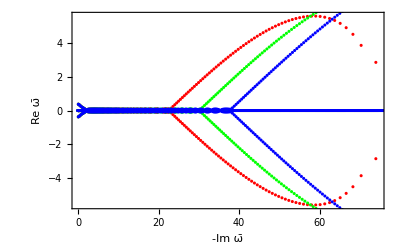

```mathematica
Axialf300a500QNMGR500=Show[f300,f400,f500]
```

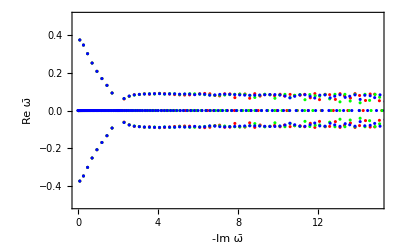

```mathematica
Axialh300a500QNMGR500=Show[h300,h400,h500]
```